# Robotics project

Mariangela Menolotto
Stefano Maugeri
Static equations and dynamic equations of a inverted pendulum on a unicycle

```mathematica
Clear["Global`*"]
```

```mathematica
egoParameters={L->0.379,r->0.13,m->21.,mc->17.9,mr->1.6,ml->1.6,l->0.248,g->9.81};
```

egoP

-Graphics3D-

## Needed

Rotation Matrix

```mathematica
Rsb[θ_]:=RotationMatrix[θ,{0,0,1}];
Rsbnegativa[θ_]:=RotationMatrix[-θ,{0,0,1}];
Rbc[ϕ_]:=RotationMatrix[ϕ, {1,0,0}];
Rbcnegativa[ϕ_]:=RotationMatrix[-ϕ, {1,0,0}];
Rsi[α_]:=RotationMatrix[α, {1,0,0}];
```

```mathematica
Rcr[θi_]:=RotationMatrix[θi, {1,0,0}];
```

```mathematica
Transpose[Rsi[α].Rsb[θ].Rbc[ϕ]]//FullSimplify//MatrixForm
```

(Cos[θ] | Cos[α] Sin[θ] | Sin[α] Sin[θ]
-Cos[ϕ] Sin[θ] | Cos[α] Cos[θ] Cos[ϕ]-Sin[α] Sin[ϕ] | Cos[θ] Cos[ϕ] Sin[α]+Cos[α] Sin[ϕ]
Sin[θ] Sin[ϕ] | -Cos[ϕ] Sin[α]-Cos[α] Cos[θ] Sin[ϕ] | Cos[α] Cos[ϕ]-Cos[θ] Sin[α] Sin[ϕ])

Visualization Functions Declaration

### Angles Parse

```mathematica
radToDeg[angle_]:=angle/Degree;
degToRad[angle_]:=angle Degree;
```

### Dynamics Plots

```mathematica
plotResults[rulesSolution_,integrationParameters_]:=Module[{},
GraphicsGrid[
{
{
Plot[x[t]/.rulesSolution,{t,0,timeOfSimulation}, PlotStyle->{Blue},ImageSize->setIimageSize,AspectRatio->1/2,AxesLabel->Automatic,PlotTheme->"Scientific",GridLines->Automatic,FrameLabel->{Style["Time (s)",FontSize->14],Style["x(t)\n(m)",FontSize->18]},RotateLabel->False],
Plot[y[t]/.rulesSolution,{t,0,timeOfSimulation},PlotStyle->{Blue},ImageSize->setIimageSize,AspectRatio->1/2,AxesLabel->Automatic,PlotTheme->"Scientific",GridLines->Automatic,FrameLabel->{Style["Time (s)",FontSize->14],Style["y(t)\n(m)",FontSize->18]},RotateLabel->False]
},
{
Plot[1/Degree θ[t]/.rulesSolution,{t,0,timeOfSimulation},PlotStyle->{Blue},ImageSize->setIimageSize,AspectRatio->1/2,AxesLabel->Automatic,PlotTheme->"Scientific",GridLines->Automatic,FrameLabel->{Style["Time (s)",FontSize->14],Style["θ(t)\n(deg)",FontSize->18]},RotateLabel->False],
Plot[1/Degree ϕ[t]/.rulesSolution,{t,0,timeOfSimulation},PlotStyle->{Blue},ImageSize->setIimageSize,AspectRatio->1/2,AxesLabel->Automatic,PlotTheme->"Scientific",GridLines->Automatic,FrameLabel->{Style["Time (s)",FontSize->14],Style["ϕ(t)\n(deg)",FontSize->18]},RotateLabel->False]
},
{
Plot[1/Degree θr[t]/.rulesSolution,{t,0,timeOfSimulation},PlotStyle->{Blue},ImageSize->setIimageSize,AspectRatio->1/2,AxesLabel->Automatic,PlotTheme->"Scientific",GridLines->Automatic,FrameLabel->{Style["Time (s)",FontSize->14],Style["θr(t)\n(deg)",FontSize->18]},RotateLabel->False],
Plot[1/Degree θl[t]/.rulesSolution,{t,0,timeOfSimulation},PlotStyle->{Blue},ImageSize->setIimageSize,AspectRatio->1/2,AxesLabel->Automatic,PlotTheme->"Scientific",GridLines->Automatic,FrameLabel->{Style["Time (s)",FontSize->14],Style["θl(t)\n(deg)",FontSize->18]},RotateLabel->False]
}
,
{
Plot[1/Degree ν2[t]/.rulesSolution,{t,0,timeOfSimulation},PlotStyle->{Blue},ImageSize->setIimageSize,AspectRatio->1/2,AxesLabel->Automatic,PlotTheme->"Scientific",GridLines->Automatic,FrameLabel->{Style["Time (s)",FontSize->14],Style["θ̇(t)\n(deg/s)",FontSize->18]},RotateLabel->False],
Plot[1/Degree ν3[t]/.rulesSolution,{t,0,timeOfSimulation},PlotStyle->{Blue},ImageSize->setIimageSize,AspectRatio->1/2,AxesLabel->Automatic,PlotTheme->"Scientific",GridLines->Automatic,FrameLabel->{Style["Time (s)",FontSize->14],Style["ϕ̇(t)\n(deg/s)",FontSize->18]},RotateLabel->False]
},
{
Plot[ν1[t]/.rulesSolution,{t,0,timeOfSimulation},PlotStyle->{Blue},ImageSize->setIimageSize,AspectRatio->1/2,AxesLabel->Automatic,PlotTheme->"Scientific",GridLines->Automatic,FrameLabel->{Style["Time (s)",FontSize->14],Style["ν1\n(m/s)",FontSize->18]},RotateLabel->False]
}
},Frame->All,Spacings->Scaled[0.15],PlotLabel->Style[{radToDeg[α],τlx,τrx}/.integrationParameters,FontSize->18]
]
]
```

### Environment and Robot Build

#### Axes and Slope

```mathematica
centerAxes := {0,0,0};
limitAxes[par_,α_]:=PlotRange->{{-0.2,5+0.2},{-0.2,par+0.2},{-0.3,0.3par+10α/(Pi/2)}};
xversor[par_]:={Thickness[.005],Arrow[{centerAxes,{par,0,0}}]};
yversor[par_]:={Thickness[.005],Arrow[{centerAxes,{0,par,0}}]};
zversor[par_]:={Thickness[.005],Arrow[{centerAxes,{0,0,par}}]};
versor[par_]:={xversor[par],yversor[par],zversor[par]};
```

```mathematica
xversorM[xor_,yor_,zor_,α_,θ_,ϕ_,color_,lengthVersor_]:={
Text[Style["x",FontSize->15,Bold,FontColor->color],{xor,yor,zor}+Rsi[α].Rsb[θ].Rbc[ϕ].{lengthVersor,0,0}+{0,0,0.2}],
color,
Thickness[.001],
Arrow[{{xor,yor,zor},{xor,yor,zor}+Rsi[α].Rsb[θ].Rbc[ϕ].{lengthVersor,0,0}}]
};
yversorM[xor_,yor_,zor_,α_,θ_,ϕ_,color_,lengthVersor_]:={
Text[Style["y",FontSize->15,Bold,FontColor->color],{xor,yor,zor}+Rsi[α].Rsb[θ].Rbc[ϕ].{0,lengthVersor,0}+{0,0,0.2}],
color,
Thickness[.001],
Arrow[{{xor,yor,zor},{xor,yor,zor}+Rsi[α].Rsb[θ].Rbc[ϕ].{0,lengthVersor,0}}]
};
zversorM[xor_,yor_,zor_,α_,θ_,ϕ_,color_,lengthVersor_]:={
Text[Style["z",FontSize->15,Bold,FontColor->color],{xor,yor,zor}+Rsi[α].Rsb[θ].Rbc[ϕ].{0,0,lengthVersor}+{0,0,0.2}],
color,
Thickness[.001],
Arrow[{{xor,yor,zor},{xor,yor,zor}+Rsi[α].Rsb[θ].Rbc[ϕ].{0,0,lengthVersor}}]
};
```

```mathematica
computeZ2[y_,α_,rad_]:=Rsi[α].{0,0,rad};
```

```mathematica
versorMoved[{xor_,yor_,zor_},α_,θ_,ϕ_,text_,xlab_,ylab_,zlab_,color_,lengthVersor_]:={
Text[Style[text,FontSize->20,Bold,FontColor->color],{xor,yor,zor}+Rsi[α].Rsb[θ].{xlab,ylab,zlab}],
xversorM[xor,yor,zor,α,θ,ϕ,color,lengthVersor],
yversorM[xor,yor,zor,α,θ,ϕ,color,lengthVersor],
zversorM[xor,yor,zor,α,θ,ϕ,color,lengthVersor]
};
```

```mathematica
rampa[scale_, α_]:={                                 Polygon[{{0,0,0},{scale,0,0},{scale,scale Cos[α],scale Sin[α]},{0,scale Cos[α], scale Sin[α]}}]}
```

```mathematica
rampa[scale_, α_,color_]:={color,Polygon[{{0,0,0},{scale,0,0},{scale,scale Cos[α],scale Sin[α]},{0,scale Cos[α], scale Sin[α]}}]}
```

```mathematica
rampa[scale_, α_,color_,yego_]:={color,Polygon[{{0,0+yego,0},{scale,0+yego,0},{scale,scale Cos[α]+yego,scale Sin[α]},{0,scale Cos[α]+yego, scale Sin[α]}}]}
```

#### Robot parts

```mathematica
baseEgo:=2 l /.egoParameters;
radiuswheel:=r/.egoParameters;
heightCM:=L/.egoParameters;
heightEGO:=1;
radiusSphere:=0.08;
```

```mathematica
wheelr[x_,y_,z_,θ_,α_,r_]:=Cylinder[{{x,y,z}+Rsi[α].Rsb[θ].{baseEgo/2,0,0},{x,y,z}+Rsi[α].Rsb[θ].{baseEgo/2+0.02,0,0}},r];
wheell[x_,y_,z_,θ_,α_,r_]:=Cylinder[{{x,y,z}-Rsi[α].Rsb[θ].{baseEgo/2,0,0},{x,y,z}-Rsi[α].Rsb[θ].{baseEgo/2+0.02,0,0}},r];
base[x_,y_,z_,θ_,ϕ_,α_]:={Thickness[.01],Line[{{x,y,z}-Rsi[α].Rsb[θ].Rbc[ϕ].{baseEgo/2,0,0},{x,y,z}+Rsi[α].Rsb[θ].Rbc[ϕ].{baseEgo/2,0,0}}]};
pendulum[x_,y_,z_,θ_,ϕ_,α_]:={Thickness[.01],Line[{{x,y,z},{x,y,z}+Rsi[α].Rsb[θ].Rbc[ϕ].{0,0,heightEGO}}]};
radiusR[x_,y_,z_,θ_,ϕ_,θr_,α_,r_]:={Thickness[.005],Red,Line[{{x,y,z}+Rsi[α].Rsb[θ].{baseEgo/2+0.02,0,0},{x,y,z}+Rsi[α].Rsb[θ].{baseEgo/2+0.02,0,0}+Rsi[α].Rsb[θ].Rbc[ϕ].Rcr[θr].{0,0,r}}]}
radiusL[x_,y_,z_,θ_,ϕ_,θl_,α_,r_]:={Thickness[.005],Red,Line[{{x,y,z}-Rsi[α].Rsb[θ].{baseEgo/2+0.02,0,0},{x,y,z}-Rsi[α].Rsb[θ].{baseEgo/2+0.02,0,0}+Rsi[α].Rsb[θ].Rbc[ϕ].Rcr[θl].{0,0,r}}]}
computeZ[y_,α_,r_]:=r/Cos[α]+y Tan[α];
drawCM[x_,y_,z_,θ_,ϕ_,α_,radSphere_]:=Sphere[{{x,y,z}+Rsi[α].Rsb[θ].Rbc[ϕ].{0,0,heightCM}},radSphere]
```

#### Robot

```mathematica
ego[x_,y_,θ_,ϕ_,θr_,θl_,α_]:={(*All the angles are in rad*)
base[x,y,computeZ[y,α,radiuswheel],θ,ϕ,α],
wheell[x,y,computeZ[y,α,radiuswheel],θ,α,radiuswheel],
wheelr[x,y,computeZ[y,α,radiuswheel],θ,α,radiuswheel],
radiusR[x,y,computeZ[y,α,radiuswheel],θ,ϕ,θr,α,radiuswheel],
radiusL[x,y,computeZ[y,α,radiuswheel],θ,ϕ,θl,α,radiuswheel],
drawCM[x,y,computeZ[y,α,radiuswheel],θ,ϕ,α,radiusSphere],
pendulum[x,y,computeZ[y,α,radiuswheel],θ,ϕ,α]
}
```

```mathematica
egoP:=Graphics3D[
{
ego[0, 0,0,0,0,0,0],
Text[Style["CM",FontSize->15,Bold,FontColor->Black],{0,0,heightCM+radiuswheel}],
(*Sphere[{0,0,heightCM+radiuswheel},0.001],*)
{Thickness[0.003], {Arrowheads[{-0.03,0.03}],Arrow[{{0.07,0,radiuswheel},{0.07,0,radiuswheel+heightCM}}]}, Text[Style["L",FontSize->15,Bold,FontColor->Black],{0.1,0,radiuswheel+heightCM/2}]},

{Thickness[0.003], {Arrowheads[{-0.03,0.03}],Arrow[{{0,0,radiuswheel+0.04},{-baseEgo/2-0.004,0,radiuswheel+0.04}}]}, Text[Style["l",FontSize->15,Bold,FontColor->Black],{-baseEgo/4-3/2*0.01,0,radiuswheel+0.08}]},

{Thickness[0.003], {Arrowheads[{-0.03,0.03}],Arrow[{{0.05-baseEgo/2-0.03,0,radiuswheel},{0.05-baseEgo/2-0.03,0,0}}]}, Text[Style["r",FontSize->15,Bold,FontColor->Black],{0.05-baseEgo/2-0.03,-0.05,0.04+radiuswheel/2}]},

Text[Style["mc",FontSize->15,Bold,FontColor->Black],{-0.05,0,heightCM/2+radiuswheel}],
Text[Style["ml",FontSize->15,Bold,FontColor->Black],{-baseEgo/2-0.08,-radiuswheel-0.01,radiuswheel}],
Text[Style["mr",FontSize->15,Bold,FontColor->Black],{+baseEgo/2+0.08,radiuswheel+0.01,0.05+radiuswheel}]

}/.egoParameters

,Boxed->False,Axes->False
]
```

### Simulator 3D Graphics - Dynamics

```mathematica
showEgoDynamicSolved[αα_,τrxvar_,τlxvar_]:=Module[{},
solEgoDyn2=computeQuasiVelocities[αα,τrxvar,τlxvar];
Return[{
Manipulate[
Column[{
Grid[{
{"α: ",radToDeg[α]/.{α->αα}},
{"τr, τl: ",{τrx,τlx}/.{α->αα,τlx->τlxvar,τrx->τrxvar}},
{"ϕ[0]",radToDeg[ϕ[0]]/.solEgoDyn2},
{"θ[0]",radToDeg[θ[0]]/.solEgoDyn2}
}
],
Graphics3D[{
versor[scale/5],
rampa[scale,0],
rampa[scale,αα],  (*Superficie in cui sta ego, il primo parametro è la larghezza, il secondo l'angolo*)
ego[x[tt]+5/2, y[tt]+scale 2/4,θ[tt], ϕ[tt],θr[tt],θl[tt],α/.{α->αα,τlx->τlxvar,τrx->τrxvar}]/.solEgoDyn2 (*Modellizzazione del robot, le coordinate si riferiscono al centro della base*)

},limitAxes[scale,αα],Axes->True,ImageSize->setIimageSize,Boxed->False
]
},Alignment->Center
],
{{scale,5, "Area size"},2,15,1,Appearance->{"Labeled"}},
{{tt,0,"Time t (sec)"},0,timeOfSimulation,Appearance->{"Labeled", "Open"},AnimationRate->1}
(*,ContentSize->{800,600}*)
],
plotResults[ solEgoDyn2,{α->αα,τrx->τrxvar,τlx->τlxvar}]
}]
];
```

### Simulator 3D Graphics - Statics

#### Definizione coppie nella grafica 3D

```mathematica
arrowτr[x_,y_,θ_,α_,τrx_]:={Thickness[0.01],LightBlue,Arrow[{{x,y,computeZ[y,α,radiuswheel]}+Rsi[α].Rsb[θ].{baseEgo/2+2+5,0,0},  {x,y,computeZ[y,α,radiuswheel]}+Rsi[α].Rsb[θ].{baseEgo/2+2+5,0,0} +    Rsi[α].Rsb[θ].{τrx,0,0} }]}
arrowτl[x_,y_,θ_,α_,τlx_]:={Thickness[0.01],LightBlue,Arrow[{{x,y,computeZ[y,α,radiuswheel]}-Rsi[α].Rsb[θ].{baseEgo/2+2+5,0,0},  {x,y,computeZ[y,α,radiuswheel]}-Rsi[α].Rsb[θ].{baseEgo/2+2+5,0,0} +    Rsi[α].Rsb[θ].{τlx,0,0} }]}
```

#### Definizione funzione di visualizzazione 3D

```mathematica
showEgoStaticSolved[α_,ϕ_,θ_,μ_,scale_]:=Module[{},
Return[{
Column[{
Grid[{
{"{τlx, τrx}",{τlx,τrx}}
}
],
Graphics3D[{
versor[scale/5],
rampa[scale,α],  (*Superficie in cui sta ego, il primo parametro è la larghezza, il secondo l'angolo*)
ego[5/2,scale/2,θ, ϕ,τrx,τlx,α],  (*Modellizzazione del robot, le coordinate si riferiscono al centro della base*)
arrowτr[scale/2,scale/2,θ,α,Clip[τrx,{-300,300}]],
arrowτl[scale/2,scale/2,θ,α,Clip[τlx,{-300,300}]]

},limitAxes[scale ,α],Axes->True,ImageSize->800
]
}/.solverForcesStaticEquation[α,ϕ,θ,μ]/.egoParameters,Alignment->Center
]
}]
]
```

Reference Systems Visualization

### 3D Simulator - References System

```mathematica
Manipulate[
Graphics3D[{
versor[1],(*Versori, il parametro indica la loro lunghezza per visibilità*)
rampa[5,Degree α,RGBColor[0,50,100]],  (*Superficie in cui sta ego, il primo parametro è la larghezza, il secondo l'angolo*)
rampa[5,0,Gray],  (*Superficie in cui sta ego, il primo parametro è la larghezza, il secondo l'angolo*)
ego[xego+2.5, yego+2.5,Degree θ,Degree ϕ,0,0,Degree α]  ,(*Modellizzazione del robot, le coordinate si riferiscono al centro della base*)
versorMoved[{0,0,0},0,0,0,"{S}",-0.1,0.3,0.3,Black,1],
versorMoved[{0,0,0},α Degree,0,0,"{I}",0.4,-0.4,0.1,Blue,1.5],
versorMoved[{xego+2.5, yego+2.5,computeZ[yego+2.5,α Degree,radiuswheel]},α Degree,θ Degree,0,"{B}",0,0,1.6,Red,1],
versorMoved[{xego+2.5, yego+2.5,computeZ[yego+2.5,α Degree,radiuswheel]},α Degree,θ Degree,ϕ Degree,"{C}",0,1,1.3,Green,1.5]
},(*limitAxes[500],*)Axes->False,ImageSize->500,Boxed->False]/.egoParameters
,{{α, 15,"Inclinazione rampa (deg)"},0,90,Appearance->{"Labeled"}},
{{xego,0,"Coord x"},-50,50,Appearance->{"Labeled"}},
{{yego,0, "Coord y"}, -50,50,Appearance->{"Labeled"}} ,(* traslazioni*)
{{ϕ,45, "ϕ (deg)"},-90,90,Appearance->{"Labeled"}},{{θ,45,"θ (deg)"},-90,90,Appearance->{"Labeled"}}
]
```

## Dynamic Equations

### Position Vector in frame {I}

#### Ruota destra

```mathematica
OB[x_,y_] :={x,y,r};
BOr[θ_]:=Rsb[θ].{l,0,0};
OOr[x_,y_,θ_] :=OB[x,y] + BOr[θ];
```

#### Ruota sinistra

```mathematica
BOl[θ_]:=Rsb[θ].{-l,0,0};
OOl[x_,y_,θ_] :=OB[x,y] + BOl[θ];
```

#### Base

```mathematica
BC[θ_,ϕ_]:=Rsb[θ].Rbc[ϕ].{0,0,L};
OC[x_,y_,θ_,ϕ_]:=OB[x,y]+BC[θ,ϕ];
```

### Linear Velocity in frame {I}

```mathematica
OOrdot[xdot_,ydot_,θdot_,θ_]:= {xdot-l Sin[θ]θdot,ydot+l Cos[θ]θdot,0};
OOldot[xdot_,ydot_,θdot_,θ_]:={xdot+l Sin[θ]θdot ,ydot-l Cos[θ] θdot,0};
OCdot[xdot_,ydot_,θdot_,ϕdot_,θ_,ϕ_]:={xdot+L Cos[θ] Sin[ϕ] θdot+L Cos[ϕ] Sin[θ] ϕdot,ydot+L Sin[θ] Sin[ϕ] θdot-L Cos[θ] Cos[ϕ] ϕdot,-L Sin[ϕ] ϕdot};(*D[OC[x[t],y[t],θ[t],ϕ[t]],t]//FullSimplify*)
```

```mathematica
vr[xdot_,ydot_,θdot_,θ_]:=OOrdot[xdot,ydot,θdot,θ];
vl[xdot_,ydot_,θdot_,θ_]:=OOldot[xdot,ydot,θdot,θ];
vc[xdot_,ydot_,θdot_,ϕdot_,θ_,ϕ_]:=OCdot[xdot,ydot,θdot,ϕdot,θ,ϕ];
```

```mathematica
Transpose[Rsb[θ[t]]].D[vc[x'[t],y'[t],θ'[t],ϕ'[t],θ[t],ϕ[t]],t]//FullSimplify//MatrixForm;
```

### Angular Velocity in frame {C}

```mathematica
θrdot[θrdotvar_]:={θrdotvar,0,0}; 
θldot[θldotvar_]:={θldotvar,0,0};
ϕdot[ϕdotvar_]:={ϕdotvar,0,0};(**)
```

### Angular Velocity in frame {I}

```mathematica
θdot[θdotvar_]:={0,0,θdotvar};
```

### Angular Velocity in frame {C}

```mathematica
ωr[ϕdotvar_,θrdotvar_,θdotvar_,ϕ_,θ_]:=ϕdot[ϕdotvar]+θrdot[θrdotvar]+Rbcnegativa[ϕ].θdot[θdotvar]   (*ω in frame {C} frame corpo*)
ωl[ϕdotvar_,θldotvar_,θdotvar_,ϕ_,θ_]:=ϕdot[ϕdotvar]+θldot[θldotvar]+Rbcnegativa[ϕ].θdot[θdotvar]
ωc[ϕdotvar_,θdotvar_,ϕ_,θ_]:=ϕdot[ϕdotvar]+Rbcnegativa[ϕ].θdot[θdotvar]
```

```mathematica
ωr[ϕ'[t],θr'[t],θ'[t],ϕ[t],θ[t]]//FullSimplify//MatrixForm;
```

```mathematica
ωc[ϕ'[t],θ'[t],ϕ[t],θ[t]]//MatrixForm
```

(ϕ'[t]
Sin[ϕ[t]] θ'[t]
Cos[ϕ[t]] θ'[t])

### Inertia Tensors

```mathematica
Ir:={{ir11,ir12,ir13},{ir21,ir22,ir23},{ir31,ir32,ir33}};
Il:={{il11,il12,il13},{il21,il22,il23},{il31,il32,il33}};
Ic:={{ic11,ic12,ic13},{ic21,ic22,ic23},{ic31,ic32,ic33}};
```

Singola ruota
Lxx = 6760133.33 Lxy = 0.00 Lxz = 0.00 
 Lyx = 0.00 Lyy = 6760133.33 Lyz = 0.00 
 Lzx = 0.00 Lzy = 0.00 Lzz = 13520000.00

Aste:
Lxx = 1988874113.74 Lxy = 0.00 Lxz = 0.00 
 Lyx = 0.00 Lyy = 2110628473.96 Lyz = 0.00 
 Lzx = 0.00 Lzy = 0.00 Lzz = 121757343.55

Ir := {{500000.00, 0, 0}, {0, 250133.33, 0}, {0, 0, 250133.33}}*10^-9;
Il := {{500000.00, 0, 0}, {0, 250133.33, 0}, {0, 0, 250133.33}}*10^-9;
Ic := {{1988874113.74, 0, 0}, {0, 2110628473.96, 0}, {0, 0, 121757343.55}}*10^-9;(*conversione da solidworks - da g*mm^2 a kg*m^2*)

```mathematica
tensIr:={ir11->13520000.00*10^-9,ir12->0,ir13->0,ir21->0,ir22->6760133.33*10^-9,ir23->0,ir31->0,ir32->0,ir33->6760133.33*10^-9};
tensIl:={il11->13520000.00*10^-9,il12->0,il13->0,il21->0,il22->6760133.33*10^-9,il23->0,il31->0,il32->0,il33->6760133.33*10^-9};
tensIc:={ic11->1988874113.74*10^-9,ic12->0,ic13->0,ic21->0,ic22->2110628473.96*10^-9,ic23->0,ic31->0,ic32->0,ic33->121757343.55 *10^-9};
```

```mathematica
Ic/.tensIc//MatrixForm
```

(1.98887 | 0 | 0
0 | 2.11063 | 0
0 | 0 | 0.121757)

```mathematica
egoTensor:={tensIr,tensIl,tensIc}//Flatten
```

```mathematica
Ir/.egoTensor//MatrixForm
```

(0.01352 | 0 | 0
0 | 0.00676013 | 0
0 | 0 | 0.00676013)

### Kinetic Energy

```mathematica
Kr[xdot_,ydot_,θdot_,θrdot_,ϕdot_,θ_,ϕ_]:=0.5*(mr*vr[xdot,ydot,θdot,θ].vr[xdot,ydot,θdot,θ]+ωr[ϕdot,θrdot,θdot,ϕ,θ].Ir.ωr[ϕdot,θrdot,θdot,ϕ,θ]);
Kl[xdot_,ydot_,θdot_,θldot_,ϕdot_,θ_,ϕ_]:=0.5*(ml*vl[xdot,ydot,θdot,θ].vl[xdot,ydot,θdot,θ]+ωl[ϕdot,θldot,θdot,ϕ,θ].Il.ωl[ϕdot,θldot,θdot,ϕ,θ]);
Kc[xdot_,ydot_,θdot_,ϕdot_,θ_,ϕ_]:=0.5*(mc*vc[xdot,ydot,θdot,ϕdot,θ,ϕ].vc[xdot,ydot,θdot,ϕdot,θ,ϕ]+ωc[ϕdot,θdot,ϕ,θ].Ic.ωc[ϕdot,θdot,ϕ,θ]);
```

```mathematica
K[xdot_,ydot_,θdot_,θrdot_,θldot_,ϕdot_,θ_,ϕ_]:=Kr[xdot,ydot,θdot,θrdot,ϕdot,θ,ϕ]+Kl[xdot,ydot,θdot,θldot,ϕdot,θ,ϕ]+Kc[xdot,ydot,θdot,ϕdot,θ,ϕ];
```

K[x’[t], y’[t], θ’[t], θr’[t], θl’[t], ϕ’[t], θ[t], ϕ[t]] //FullSimplify// MatrixForm		(*debug*)

### Potential Energy

```mathematica
gt:={0,0,-g}
```

```mathematica
Ur[x_,y_,θ_]:=-mr*gt.Rsi[α].OOr[x,y,θ];
Ul[x_,y_,θ_]:=-ml*gt.Rsi[α].OOl[x,y,θ];
Uc[x_,y_,θ_,ϕ_]:=-mc*gt.Rsi[α].OC[x,y,θ,ϕ];
```

```mathematica
U[x_,y_,θ_,ϕ_]:=Ur[x,y,θ]+Ul[x,y,θ]+Uc[x,y,θ,ϕ];
```

```mathematica
U[x,y,θ,ϕ]//MatrixForm
```

-ml (-g r Cos[α]-g Sin[α] (y-l Sin[θ]))-mr (-g r Cos[α]-g Sin[α] (y+l Sin[θ]))-mc (-g Cos[α] (r+L Cos[ϕ])-g Sin[α] (y-L Cos[θ] Sin[ϕ]))

### Vector Definitions (q, q̇, q^(..) )

```mathematica
coords={x[t],y[t],θ[t],ϕ[t],θr[t],θl[t]};
coordsDer={x'[t],y'[t],θ'[t],ϕ'[t],θr'[t],θl'[t]};
coordsAcc={x''[t], y''[t], θ''[t], ϕ''[t], θr''[t], θl''[t]};
```

### Generalized Forces (τ in frame {C})

```mathematica
τr[τrx_]:={τrx,0,0};(*In frame {C}*)
τl[τlx_]:={+τlx,0,0};
```

```mathematica
Qx:=0;
```

```mathematica
Qy:=0;
```

```mathematica
Qθ[θdot_,θrdot_,θldot_,ϕdot_,θ_,ϕ_,τrx_,τlx_]:=τr[τrx].D[ωr[ϕdot,θrdot,θdot,ϕ,θ],θdot]+
τl[τlx].D[ωl[ϕdot,θldot,θdot,ϕ,θ],θdot];
```

```mathematica
Qϕ:=0;
```

```mathematica
Qθr[θrdot_,θdot_,ϕdot_,θ_,ϕ_,τrx_]:=τr[τrx].D[ωr[ϕdot,θrdot,θdot,ϕ,θ],θrdot];
```

```mathematica
Qθl[θldot_,θdot_,ϕdot_,θ_,ϕ_,τlx_]:=τl[τlx].D[ωl[ϕdot,θldot,θdot,ϕ,θ],θldot];
```

```mathematica
Q[θdot_,θrdot_,θldot_,ϕdot_,θ_,ϕ_,τrx_,τlx_]:={
Qx,
Qy,
Qθ[θdot,θrdot,θldot,ϕdot,θ,ϕ,τrx,τlx],
Qϕ,
Qθr[θrdot,θdot,ϕdot,θ,ϕ,τrx],
Qθl[θldot,θdot,ϕdot,θ,ϕ,τlx]
};
```

```mathematica
Q[θ'[t],θr'[t],θl'[t],ϕ'[t],θ[t],ϕ[t],τrx,τlx]// MatrixForm  (*debug*)
```

(0
0
0
0
τrx
τlx)

### Constraint Equations (A Pfaffiana)

```mathematica
Cross[Rsb[θ[t]].Rbc[ϕ[t]].ωr[ϕ'[t],θr'[t],θ'[t],ϕ[t],θ[t]],{0,0,-r}]+vr[x'[t],y'[t],θ'[t],θ[t]]//FullSimplify//MatrixForm
```

(x'[t]-Sin[θ[t]] (l θ'[t]+r (θr'[t]+ϕ'[t]))
y'[t]+Cos[θ[t]] (l θ'[t]+r (θr'[t]+ϕ'[t]))
0)

```mathematica
Cross[Rsb[θ[t]].Rbc[ϕ[t]].ωl[ϕ'[t],θl'[t],θ'[t],ϕ[t],θ[t]],{0,0,-r}]+vl[x'[t],y'[t],θ'[t],θ[t]]//FullSimplify//MatrixForm
```

(x'[t]+Sin[θ[t]] (l θ'[t]-r (θl'[t]+ϕ'[t]))
y'[t]+Cos[θ[t]] (-l θ'[t]+r (θl'[t]+ϕ'[t]))
0)

```mathematica
Apfaf[θ_]:={
{Cos[θ],Sin[θ],0,0,0,0},
{1,0,-l Sin[θ],-r Sin[θ],-r Sin[θ],0},
{0,1,l Cos[θ],r Cos[θ],r Cos[θ],0},
{1,0,l Sin[θ],-r Sin[θ],0,-r Sin[θ]},
{0,1,-l Cos[θ],r Cos[θ],0,r Cos[θ]}
};
```

```mathematica
Apfaf[θ]//MatrixForm
```

(Cos[θ] | Sin[θ] | 0 | 0 | 0 | 0
1 | 0 | -l Sin[θ] | -r Sin[θ] | -r Sin[θ] | 0
0 | 1 | l Cos[θ] | r Cos[θ] | r Cos[θ] | 0
1 | 0 | l Sin[θ] | -r Sin[θ] | 0 | -r Sin[θ]
0 | 1 | -l Cos[θ] | r Cos[θ] | 0 | r Cos[θ])

```mathematica
MatrixRank[Apfaf[θ]]
```

3

```mathematica
QminusApfaf[θdot_,θrdot_,θldot_,ϕdot_,θ_,ϕ_,τrx_,τlx_,λ1_,λ2_,λ3_,λ4_,λ5_]:=Q[θdot,θrdot,θldot,ϕdot,θ,ϕ,τrx,τlx]-Transpose[Apfaf[θ]].{λ1,λ2,λ3,λ4,λ5};
```

```mathematica
QminusApfaf[θ'[t],θr'[t],θl'[t],ϕ'[t],θ[t],ϕ[t],τrx,τlx,λ1,λ2,λ3,λ4,λ5](*debug*)//MatrixForm;
```

### [Unused] - Dynamic Equations - Lagrangian Approach

```mathematica
Lagrangiana[xdot_,ydot_,θdot_,θrdot_,θldot_,ϕdot_,θ_,ϕ_,x_,y_]:=K[xdot,ydot,θdot,θrdot,θldot,ϕdot,θ,ϕ]-U[x,y,θ,ϕ];
```

```mathematica
EquazioneDinamica1[xdot_,ydot_,θdot_,ϕdot_,θrdot_,θldot_,θ_,θr_,θl_,ϕ_,τrx_,τlx_,λ1_,λ2_,λ3_,λ4_,λ5_,x_,y_]:=(D[D[Lagrangiana[xdot,ydot,θdot,θrdot,θldot,ϕdot,θ,ϕ,x,y],D[coords[[1]],t]],t]-D[Lagrangiana[xdot,ydot,θdot,θrdot,θldot,ϕdot,θ,ϕ,x,y],coords[[1]]])-
 QminusApfaf[θdot,θrdot,θldot,ϕdot,θ,ϕ,τrx,τlx,λ1,λ2,λ3,λ4,λ5][[1]];

EquazioneDinamica2[xdot_,ydot_,θdot_,ϕdot_,θrdot_,θldot_,θ_,θr_,θl_,ϕ_,τrx_,τlx_,λ1_,λ2_,λ3_,λ4_,λ5_,x_,y_]:=(D[D[Lagrangiana[xdot,ydot,θdot,θrdot,θldot,ϕdot,θ,ϕ,x,y],D[coords[[2]],t]],t]-D[Lagrangiana[xdot,ydot,θdot,θrdot,θldot,ϕdot,θ,ϕ,x,y],coords[[2]]])-
QminusApfaf[θdot,θrdot,θldot,ϕdot,θ,ϕ,τrx,τlx,λ1,λ2,λ3,λ4,λ5][[2]];

EquazioneDinamica3[xdot_,ydot_,θdot_,ϕdot_,θrdot_,θldot_,θ_,θr_,θl_,ϕ_,τrx_,τlx_,λ1_,λ2_,λ3_,λ4_,λ5_,x_,y_]:=(D[D[Lagrangiana[xdot,ydot,θdot,θrdot,θldot,ϕdot,θ,ϕ,x,y],D[coords[[3]],t]],t]-D[Lagrangiana[xdot,ydot,θdot,θrdot,θldot,ϕdot,θ,ϕ,x,y],coords[[3]]]) -
QminusApfaf[θdot,θrdot,θldot,ϕdot,θ,ϕ,τrx,τlx,λ1,λ2,λ3,λ4,λ5][[3]];

EquazioneDinamica4[xdot_,ydot_,θdot_,ϕdot_,θrdot_,θldot_,θ_,θr_,θl_,ϕ_,τrx_,τlx_,λ1_,λ2_,λ3_,λ4_,λ5_,x_,y_]:=(D[D[Lagrangiana[xdot,ydot,θdot,θrdot,θldot,ϕdot,θ,ϕ,x,y],D[coords[[4]],t]],t]-D[Lagrangiana[xdot,ydot,θdot,θrdot,θldot,ϕdot,θ,ϕ,x,y],coords[[4]]]) -
QminusApfaf[θdot,θrdot,θldot,ϕdot,θ,ϕ,τrx,τlx,λ1,λ2,λ3,λ4,λ5][[4]];

EquazioneDinamica5[xdot_,ydot_,θdot_,ϕdot_,θrdot_,θldot_,θ_,θr_,θl_,ϕ_,τrx_,τlx_,λ1_,λ2_,λ3_,λ4_,λ5_,x_,y_]:=(D[D[Lagrangiana[xdot,ydot,θdot,θrdot,θldot,ϕdot,θ,ϕ,x,y],D[coords[[5]],t]],t]-D[Lagrangiana[xdot,ydot,θdot,θrdot,θldot,ϕdot,θ,ϕ,x,y],coords[[5]]])-
QminusApfaf[θdot,θrdot,θldot,ϕdot,θ,ϕ,τrx,τlx,λ1,λ2,λ3,λ4,λ5][[5]];

EquazioneDinamica6[xdot_,ydot_,θdot_,ϕdot_,θrdot_,θldot_,θ_,θr_,θl_,ϕ_,τrx_,τlx_,λ1_,λ2_,λ3_,λ4_,λ5_,x_,y_]:=(D[D[Lagrangiana[xdot,ydot,θdot,θrdot,θldot,ϕdot,θ,ϕ,x,y],D[coords[[6]],t]],t]-D[Lagrangiana[xdot,ydot,θdot,θrdot,θldot,ϕdot,θ,ϕ,x,y],coords[[6]]])-
QminusApfaf[θdot,θrdot,θldot,ϕdot,θ,ϕ,τrx,τlx,λ1,λ2,λ3,λ4,λ5][[6]];
```

```mathematica
EquazioneDinamica[xdot_,ydot_,θdot_,ϕdot_,θrdot_,θldot_,θ_,θr_,θl_,ϕ_,τrx_,τlx_,λ1_,λ2_,λ3_,λ4_,λ5_,x_,y_]:={
EquazioneDinamica1[xdot,ydot,θdot,ϕdot,θrdot,θldot,θ,θr,θl,ϕ,τrx,τlx,λ1,λ2,λ3,λ4,λ5,x,y]==0,
EquazioneDinamica2[xdot,ydot,θdot,ϕdot,θrdot,θldot,θ,θr,θl,ϕ,τrx,τlx,λ1,λ2,λ3,λ4,λ5,x,y]==0,
EquazioneDinamica3[xdot,ydot,θdot,ϕdot,θrdot,θldot,θ,θr,θl,ϕ,τrx,τlx,λ1,λ2,λ3,λ4,λ5,x,y]==0,
EquazioneDinamica4[xdot,ydot,θdot,ϕdot,θrdot,θldot,θ,θr,θl,ϕ,τrx,τlx,λ1,λ2,λ3,λ4,λ5,x,y]==0,
EquazioneDinamica5[xdot,ydot,θdot,ϕdot,θrdot,θldot,θ,θr,θl,ϕ,τrx,τlx,λ1,λ2,λ3,λ4,λ5,x,y]==0,
EquazioneDinamica6[xdot,ydot,θdot,ϕdot,θrdot,θldot,θ,θr,θl,ϕ,τrx,τlx,λ1,λ2,λ3,λ4,λ5,x,y]==0
}
```

```mathematica
EquazioneDinamicaSenzaZeri[xdot_,ydot_,θdot_,ϕdot_,θrdot_,θldot_,θ_,θr_,θl_,ϕ_,τrx_,τlx_,λ1_,λ2_,λ3_,λ4_,λ5_,x_,y_]:={
EquazioneDinamica1[xdot,ydot,θdot,ϕdot,θrdot,θldot,θ,θr,θl,ϕ,τrx,τlx,λ1,λ2,λ3,λ4,λ5,x,y],
EquazioneDinamica2[xdot,ydot,θdot,ϕdot,θrdot,θldot,θ,θr,θl,ϕ,τrx,τlx,λ1,λ2,λ3,λ4,λ5,x,y],
EquazioneDinamica3[xdot,ydot,θdot,ϕdot,θrdot,θldot,θ,θr,θl,ϕ,τrx,τlx,λ1,λ2,λ3,λ4,λ5,x,y],
EquazioneDinamica4[xdot,ydot,θdot,ϕdot,θrdot,θldot,θ,θr,θl,ϕ,τrx,τlx,λ1,λ2,λ3,λ4,λ5,x,y],
EquazioneDinamica5[xdot,ydot,θdot,ϕdot,θrdot,θldot,θ,θr,θl,ϕ,τrx,τlx,λ1,λ2,λ3,λ4,λ5,x,y],
EquazioneDinamica6[xdot,ydot,θdot,ϕdot,θrdot,θldot,θ,θr,θl,ϕ,τrx,τlx,λ1,λ2,λ3,λ4,λ5,x,y]
}
```

```mathematica
constraintsEquations[θ_]:={
Apfaf[θ][[1]].coordsDer==0,
Apfaf[θ][[2]].coordsDer==0,
Apfaf[θ][[3]].coordsDer==0,
Apfaf[θ][[4]].coordsDer==0,
Apfaf[θ][[5]].coordsDer==0
}
```

### Print Dynamic Equations

eq1 = EquazioneDinamica1[x'[t], y'[t], θ'[t], ϕ'[t], θr'[t], θl'[t], θ[t], θr[t], θl[t], ϕ[t], τrx, τlx, λ1[t], λ2[t], λ3[t], λ4[t], λ5[t], x[t], y[t]] == 0 /. egoParameters /. egoTensor // FullSimplify

Cos[θ[t]] λ1[t]+λ2[t]+λ4[t]-7.5 Sin[θ[t]] Sin[ϕ[t]] θ'[t]^2+15. Cos[θ[t]] Cos[ϕ[t]] θ'[t] ϕ'[t]-7.5 Sin[θ[t]] Sin[ϕ[t]] ϕ'[t]^2+21. x''[t]+7.5 Cos[θ[t]] Sin[ϕ[t]] θ''[t]+7.5 Cos[ϕ[t]] Sin[θ[t]] ϕ''[t]==0

Cos[θ[t]] λ1[t]+λ2[t]+λ4[t]-7.5 Sin[θ[t]] Sin[ϕ[t]] θ'[t]^2+15. Cos[θ[t]] Cos[ϕ[t]] θ'[t] ϕ'[t]-7.5 Sin[θ[t]] Sin[ϕ[t]] ϕ'[t]^2+21. x''[t]+7.5 Cos[θ[t]] Sin[ϕ[t]] θ''[t]+7.5 Cos[ϕ[t]] Sin[θ[t]] ϕ''[t]==0

eq2 = EquazioneDinamica2[x'[t], y'[t], θ'[t], ϕ'[t], θr'[t], θl'[t], θ[t], θr[t], θl[t], ϕ[t], τrx, τlx, λ1[t], λ2[t], λ3[t], λ4[t], λ5[t], x[t], y[t]] == 0 /. egoParameters /. egoTensor // FullSimplify

1. Sin[α]+0.00485413 Sin[θ[t]] λ1[t]+0.00485413 λ3[t]+0.00485413 λ5[t]+0.036406 Cos[θ[t]] Sin[ϕ[t]] θ'[t]^2+0.072812 Cos[ϕ[t]] Sin[θ[t]] θ'[t] ϕ'[t]+0.101937 y''[t]+Sin[ϕ[t]] (0.036406 Cos[θ[t]] ϕ'[t]^2+0.036406 Sin[θ[t]] θ''[t])==0.036406 Cos[θ[t]] Cos[ϕ[t]] ϕ''[t]

eq3 = EquazioneDinamica3[x'[t], y'[t], θ'[t], ϕ'[t], θr'[t], θl'[t], θ[t], θr[t], θl[t], ϕ[t], τrx, τlx, λ1[t], λ2[t], λ3[t], λ4[t], λ5[t], x[t], y[t]] == 0 /. egoParameters /. egoTensor // FullSimplify

1. Sin[α] Sin[θ[t]] Sin[ϕ[t]]+0.00917045 Sin[2 ϕ[t]] θ'[t] ϕ'[t]+Cos[θ[t]] (0.00339789 λ3[t]-0.00339789 λ5[t]+0.101937 Sin[ϕ[t]] x''[t])+Sin[θ[t]] (-0.00339789 λ2[t]+0.00339789 λ4[t]+0.101937 Sin[ϕ[t]] y''[t])+(0.0526321-0.00458523 Cos[2 ϕ[t]]) θ''[t]==0

1. Sin[α] Sin[θ[t]] Sin[ϕ[t]]+0.0498291 Sin[2 ϕ[t]] θ'[t] ϕ'[t]+Cos[θ[t]] (0.00339789 λ3[t]-0.00339789 λ5[t]+0.101937 Sin[ϕ[t]] x''[t])+Sin[θ[t]] (-0.00339789 λ2[t]+0.00339789 λ4[t]+0.101937 Sin[ϕ[t]] y''[t])+(0.0729614-0.0249145 Cos[2 ϕ[t]]) θ''[t]==0

eq4 = EquazioneDinamica4[x'[t], y'[t], θ'[t], ϕ'[t], θr'[t], θl'[t], θ[t], θr[t], θl[t], ϕ[t], τrx, τlx, λ1[t], λ2[t], λ3[t], λ4[t], λ5[t], x[t], y[t]] == 0 /. egoParameters /. egoTensor // FullSimplify

(0.-3.55271×10^-15 ⅈ) Cos[α-θ[t]] Cos[ϕ[t]]+(-73.575 Cos[α]-3.55271×10^-15 Sin[α] Sin[θ[t]]-(0.+3.55271×10^-15 ⅈ) Sin[α+θ[t]]) Sin[ϕ[t]]+Sin[θ[t]] (-0.13 λ4[t]+7.5 Cos[ϕ[t]] x''[t])+Cos[θ[t]] (0.13 λ3[t]+0.13 λ5[t]-7.5 Cos[ϕ[t]] y''[t])+0.0009375 θl''[t]+0.0009375 θr''[t]+6.82716 ϕ''[t]==73.575 Cos[θ[t]] Cos[ϕ[t]] Sin[α]+3.55271×10^-15 Cos[α] Cos[ϕ[t]] Sin[θ[t]]+0.13 Sin[θ[t]] λ2[t]+0.337358 Sin[2 ϕ[t]] θ'[t]^2

(0.+4.8287×10^-17 ⅈ) Cos[α-θ[t]] Cos[ϕ[t]]+1. Cos[θ[t]] Cos[ϕ[t]] Sin[α]+4.8287×10^-17 Cos[α] Cos[ϕ[t]] Sin[θ[t]]+(1. Cos[α]+4.8287×10^-17 Sin[α] Sin[θ[t]]+(0.+4.8287×10^-17 ⅈ) Sin[α+θ[t]]) Sin[ϕ[t]]+0.0249145 Sin[2 ϕ[t]] θ'[t]^2+Cos[ϕ[t]] (-0.101937 Sin[θ[t]] x''[t]+0.101937 Cos[θ[t]] y''[t])==0.0521078 ϕ''[t]

eq5 = EquazioneDinamica5[x'[t], y'[t], θ'[t], ϕ'[t], θr'[t], θl'[t], θ[t], θr[t], θl[t], ϕ[t], τrx, τlx, λ1[t], λ2[t], λ3[t], λ4[t], λ5[t], x[t], y[t]] == 0 /. egoParameters /. egoTensor // FullSimplify

0.13 Cos[θ[t]] λ3[t]+0.0009375 (θr''[t]+ϕ''[t])==τrx+0.13 Sin[θ[t]] λ2[t]

0.13 Cos[θ[t]] λ3[t]+0.0009375 θr''[t]==τrx+0.13 Sin[θ[t]] λ2[t]

eq6 = EquazioneDinamica6[x'[t], y'[t], θ'[t], ϕ'[t], θr'[t], θl'[t], θ[t], θr[t], θl[t], ϕ[t], τrx, τlx, λ1[t], λ2[t], λ3[t], λ4[t], λ5[t], x[t], y[t]] == 0 /. egoParameters /. egoTensor // FullSimplify

0.13 Cos[θ[t]] λ5[t]+0.0009375 (θl''[t]+ϕ''[t])==τlx+0.13 Sin[θ[t]] λ4[t]

0.13 Cos[θ[t]] λ5[t]+0.0009375 θl''[t]==τlx+0.13 Sin[θ[t]] λ4[t]

EquazioneDinamica[x'[t], y'[t], θ'[t], ϕ'[t], θr'[t], θl'[t], θ[t], θr[t], θl[t], ϕ[t], τrx, τlx, λ1[t], λ2[t], λ3[t], λ4[t], λ5[t], x[t], y[t]] /. egoParameters /. egoTensor // FullSimplify // MatrixForm

(Cos[θ[t]] λ1[t]+λ2[t]+λ4[t]-7.5 Sin[θ[t]] Sin[ϕ[t]] θ'[t]^2+15. Cos[θ[t]] Cos[ϕ[t]] θ'[t] ϕ'[t]-7.5 Sin[θ[t]] Sin[ϕ[t]] ϕ'[t]^2+21. x''[t]+7.5 Cos[θ[t]] Sin[ϕ[t]] θ''[t]+7.5 Cos[ϕ[t]] Sin[θ[t]] ϕ''[t]==0
1. Sin[α]+0.00485413 Sin[θ[t]] λ1[t]+0.00485413 λ3[t]+0.00485413 λ5[t]+0.036406 Cos[θ[t]] Sin[ϕ[t]] θ'[t]^2+0.072812 Cos[ϕ[t]] Sin[θ[t]] θ'[t] ϕ'[t]+0.101937 y''[t]+Sin[ϕ[t]] (0.036406 Cos[θ[t]] ϕ'[t]^2+0.036406 Sin[θ[t]] θ''[t])==0.036406 Cos[θ[t]] Cos[ϕ[t]] ϕ''[t]
1. Sin[α] Sin[θ[t]] Sin[ϕ[t]]+0.0498291 Sin[2 ϕ[t]] θ'[t] ϕ'[t]+Cos[θ[t]] (0.00339789 λ3[t]-0.00339789 λ5[t]+0.101937 Sin[ϕ[t]] x''[t])+Sin[θ[t]] (-0.00339789 λ2[t]+0.00339789 λ4[t]+0.101937 Sin[ϕ[t]] y''[t])+(0.0729614-0.0249145 Cos[2 ϕ[t]]) θ''[t]==0
(0.+4.8287×10^-17 ⅈ) Cos[α-θ[t]] Cos[ϕ[t]]+1. Cos[θ[t]] Cos[ϕ[t]] Sin[α]+4.8287×10^-17 Cos[α] Cos[ϕ[t]] Sin[θ[t]]+(1. Cos[α]+4.8287×10^-17 Sin[α] Sin[θ[t]]+(0.+4.8287×10^-17 ⅈ) Sin[α+θ[t]]) Sin[ϕ[t]]+0.0249145 Sin[2 ϕ[t]] θ'[t]^2+Cos[ϕ[t]] (-0.101937 Sin[θ[t]] x''[t]+0.101937 Cos[θ[t]] y''[t])==0.0521078 ϕ''[t]
0.13 Cos[θ[t]] λ3[t]+0.0009375 θr''[t]==τrx+0.13 Sin[θ[t]] λ2[t]
0.13 Cos[θ[t]] λ5[t]+0.0009375 θl''[t]==τlx+0.13 Sin[θ[t]] λ4[t])

## Compute Numeric Solution with Quasi Velocity method

From Equations:
B(q) q^(..) + C(q, q̇)q̇+G(q)+A^T(q)λ=Q(t)
       A(q)q̇=0
We Obatin:
ν̇ =(S^T B S)^-1 S^T[Q-(B Ṡ+C S)ν-G]
       q̇ =S ν

```mathematica
ν[ν1_,ν2_,ν3_]:={ν1,ν2,ν3}
```

```mathematica
νdot[ν1dot_,ν2dot_,ν3dot_]:={ν1dot,ν2dot,ν3dot}
```

### B Matrix

```mathematica
getMatrixFromSystem[system_,vectCoords_]:=(Normal[CoefficientArrays[system,vectCoords]][[2]])
```

```mathematica
Jvr[xdot_,ydot_,θdot_,θ_]:=getMatrixFromSystem[OOrdot[xdot,ydot,θdot,θ],coordsDer]
Jvl[xdot_,ydot_,θdot_,θ_]:=getMatrixFromSystem[OOldot[xdot,ydot,θdot,θ],coordsDer];
Jvc[xdot_,ydot_,θdot_,ϕdot_,θ_,ϕ_]:=getMatrixFromSystem[OCdot[xdot,ydot,θdot,ϕdot,θ,ϕ],coordsDer];
Jωr[ϕdot_,θrdotvar_,θdotvar_,ϕ_,θ_]:=getMatrixFromSystem[ωr[ϕdot,θrdotvar,θdotvar,ϕ,θ],coordsDer];
Jωl[ϕdot_,θldotvar_,θdotvar_,ϕ_,θ_]:=getMatrixFromSystem[ωl[ϕdot,θldotvar,θdotvar,ϕ,θ],coordsDer];
Jωc[ϕdotvar_,θdotvar_,ϕ_,θ_]:=getMatrixFromSystem[ωc[ϕdotvar,θdotvar,ϕ,θ],coordsDer];
```

```mathematica
BB[xdot_,ydot_,θdot_,ϕdot_,θrdot_,θldot_,θ_,ϕ_]:=mr*Transpose[Jvr[xdot,ydot,θdot,θ]].Jvr[xdot,ydot,θdot,θ]+Transpose[Jωr[ϕdot,θrdot,θdot,ϕ,θ]].Ir.Jωr[ϕdot,θrdot,θdot,ϕ,θ]+ml*Transpose[Jvl[xdot,ydot,θdot,θ]].Jvl[xdot,ydot,θdot,θ]+Transpose[Jωl[ϕdot,θldot,θdot,ϕ,θ]].Il.Jωl[ϕdot,θldot,θdot,ϕ,θ]+mc*Transpose[Jvc[xdot,ydot,θdot,ϕdot,θ,ϕ]].Jvc[xdot,ydot,θdot,ϕdot,θ,ϕ]+Transpose[Jωc[ϕdot,θdot,ϕ,θ]].Ic.Jωc[ϕdot,θdot,ϕ,θ];
```

```mathematica
BB[x'[t],y'[t],θ'[t],ϕ'[t],θr'[t],θl'[t],θ[t],ϕ[t]]/.egoParameters/.egoTensor//FullSimplify//MatrixForm
```

(21.1 | 0 | 6.7841 Cos[θ[t]] Sin[ϕ[t]] | 6.7841 Cos[ϕ[t]] Sin[θ[t]] | 0 | 0
0 | 21.1 | 6.7841 Sin[θ[t]] Sin[ϕ[t]] | -6.7841 Cos[θ[t]] Cos[ϕ[t]] | 0 | 0
6.7841 Cos[θ[t]] Sin[ϕ[t]] | 6.7841 Sin[θ[t]] Sin[ϕ[t]] | 2.61211-2.28002 Cos[2 ϕ[t]] | 0 | 0 | 0
6.7841 Cos[ϕ[t]] Sin[θ[t]] | -6.7841 Cos[θ[t]] Cos[ϕ[t]] | 0 | 4.58709 | 0.01352 | 0.01352
0 | 0 | 0 | 0.01352 | 0.01352 | 0
0 | 0 | 0 | 0.01352 | 0 | 0.01352)

```mathematica
Jωl[ϕ'[t],θl'[t],θ'[t],ϕ[t],θ[t]]//MatrixForm
```

(0 | 0 | 0 | 1 | 0 | 1
0 | 0 | Sin[ϕ[t]] | 0 | 0 | 0
0 | 0 | Cos[ϕ[t]] | 0 | 0 | 0)

### G Vector

```mathematica
U[x[t],y[t],θ[t],ϕ[t]]/.egoParameters//FullSimplify
```

Cos[α] (26.9088+66.552 Cos[ϕ[t]])-66.552 Cos[θ[t]] Sin[α] Sin[ϕ[t]]+206.991 Sin[α] y[t]

```mathematica
D[U[x[t],y[t],θ[t],ϕ[t]],y[t]]/.egoParameters
```

206.991 Sin[α]

```mathematica
Gx[x_,y_,θ_,ϕ_]:=D[U[x,y,θ,ϕ],x]
Gy[x_,y_,θ_,ϕ_]:=D[U[x,y,θ,ϕ],y]
Gθ[x_,y_,θ_,ϕ_]:=D[U[x,y,θ,ϕ],θ]
Gϕ[x_,y_,θ_,ϕ_]:=D[U[x,y,θ,ϕ],ϕ]
Gθr[x_,y_,θ_,ϕ_,θr_]:=D[U[x,y,θ,ϕ],θr]
Gθl[x_,y_,θ_,ϕ_,θl_]:=D[U[x,y,θ,ϕ],θl]
```

```mathematica
GG[x_,y_,θ_,ϕ_,θr_,θl_]:={
Gx[x,y,θ,ϕ],
Gy[x,y,θ,ϕ],
Gθ[x,y,θ,ϕ],
Gϕ[x,y,θ,ϕ],
Gθr[x,y,θ,ϕ,θr],
Gθl[x,y,θ,ϕ,θr]
}
```

```mathematica
GG[x[t],y[t],θ[t],ϕ[t],θr[t],θl[t]]/.egoParameters//FullSimplify//MatrixForm
```

(0
206.991 Sin[α]
Sin[α] (-4.44089×10^-16 Cos[θ[t]]+66.552 Sin[θ[t]] Sin[ϕ[t]])
-66.552 Cos[θ[t]] Cos[ϕ[t]] Sin[α]-66.552 Cos[α] Sin[ϕ[t]]
0
0)

```mathematica
GGjac[xdot_,ydot_,θdot_,ϕdot_,θ_,ϕ_]:=-mr*Rsi[-α].gt.(Jvr[xdot,ydot,θdot,θ]+Jvl[xdot,ydot,θdot,θ])-mc*Rsi[-α].gt.Jvc[xdot,ydot,θdot,ϕdot,θ,ϕ]
```

```mathematica
GGjac[x'[t],y'[t],θ'[t],ϕ'[t],θ[t],ϕ[t]]/.egoParameters//FullSimplify//MatrixForm
```

(0
206.991 Sin[α]
66.552 Sin[α] Sin[θ[t]] Sin[ϕ[t]]
-66.552 Cos[θ[t]] Cos[ϕ[t]] Sin[α]-66.552 Cos[α] Sin[ϕ[t]]
0
0)

### C Matrix

```mathematica
BB[x'[t],y'[t],θ'[t],ϕ'[t],θr'[t],θl'[t],θ[t],ϕ[t]]/.egoParameters/.egoTensor//FullSimplify//MatrixForm
```

(21.1 | 0 | 6.7841 Cos[θ[t]] Sin[ϕ[t]] | 6.7841 Cos[ϕ[t]] Sin[θ[t]] | 0 | 0
0 | 21.1 | 6.7841 Sin[θ[t]] Sin[ϕ[t]] | -6.7841 Cos[θ[t]] Cos[ϕ[t]] | 0 | 0
6.7841 Cos[θ[t]] Sin[ϕ[t]] | 6.7841 Sin[θ[t]] Sin[ϕ[t]] | 2.61211-2.28002 Cos[2 ϕ[t]] | 0 | 0 | 0
6.7841 Cos[ϕ[t]] Sin[θ[t]] | -6.7841 Cos[θ[t]] Cos[ϕ[t]] | 0 | 4.58709 | 0.01352 | 0.01352
0 | 0 | 0 | 0.01352 | 0.01352 | 0
0 | 0 | 0 | 0.01352 | 0 | 0.01352)

```mathematica
cijk[xdot_,ydot_,θdot_,ϕdot_,θrdot_,θldot_,θ_,ϕ_,i_,j_,k_]:=0.5*
(D[BB[xdot,ydot,θdot,ϕdot,θrdot,θldot,θ,ϕ][[i,j]],coords[[k]]]+D[BB[xdot,ydot,θdot,ϕdot,θrdot,θldot,θ,ϕ][[i,k]],coords[[j]]]-D[BB[xdot,ydot,θdot,ϕdot,θrdot,θldot,θ,ϕ][[j,k]],coords[[i]]])coordsDer[[k]]
```

```mathematica
cijk[xdot_,ydot_,θdot_,ϕdot_,θrdot_,θldot_,θ_,ϕ_,i_,j_,k_,prova_]:=0.5*(deBB[i,j,coords[[k]]]+deBB[i,k,coords[[j]]]-deBB[j,k,coords[[i]]])coordsDer[[k]]
```

```mathematica
CCoriolisToBuild=ConstantArray[0,{6,6}];
```

For[i = 1, i < 7, i++,
    For[j = 1, j < 7, j++,
      item = 0;
      For[k = 1, k < 7, k++,
        item = item + cijk[x'[t], y'[t], θ'[t], ϕ'[t], θr'[t], θl'[t], θ[t], ϕ[t], i, j, k];
        ];
      CCoriolisToBuild[[i, j]] = item;
      ]
    ];

```mathematica
buildCor[xdot_,ydot_,θdot_,ϕdot_,θrdot_,θldot_,θ_,ϕ_]:=Module[{},
For[i=1,i<7,i++,
For[j=1,j<7,j++,
item=0;
For[k=1,k<7,k++,
item=item+cijk[xdot,ydot,θdot,ϕdot,θrdot,θldot,θ,ϕ,i,j,k];
];
CCoriolisToBuild[[i,j]]=item;
]
]; Return[CCoriolisToBuild]
]
```

```mathematica
provaCor[xdot_,ydot_,θdot_,ϕdot_,θrdot_,θldot_,θ_,ϕ_]:=buildCor[xdot,ydot,θdot,ϕdot,θrdot,θldot,θ,ϕ]
```

```mathematica
provaCor[x'[t],y'[t],θ'[t],ϕ'[t],θr'[t],θl'[t],θ[t],ϕ[t]]//FullSimplify;
```

```mathematica
CCoriolis[xdot_,ydot_,θdot_,ϕdot_,θrdot_,θldot_,θ_,ϕ_]:={{0.,0.,1. (l (ml-1. mr) Cos[θ]-1. L mc Sin[θ] Sin[ϕ]) θdot+1. L mc Cos[θ] Cos[ϕ] ϕdot,L mc (1. Cos[θ] Cos[ϕ] θdot-1. Sin[θ] Sin[ϕ] ϕdot),0.,0.},{0.,0.,1. (l (ml-1. mr) Sin[θ]+L mc Cos[θ] Sin[ϕ]) θdot+1. L mc Cos[ϕ] Sin[θ] ϕdot,L mc (1. Cos[ϕ] Sin[θ] θdot+1. Cos[θ] Sin[ϕ] ϕdot),0.,0.},{0.,0.,-0.5 ((-1. ic23-1. ic32-1. il23-1. il32-1. ir23-1. ir32) Cos[2 ϕ]+(-1. ic22+1. ic33-1. il22+1. il33-1. ir22+1. ir33-1. L^2 mc) Sin[2 ϕ]) ϕdot,((0.5 ic23+0.5 ic32+0.5 il23+0.5 il32+0.5 ir23+0.5 ir32) Cos[2 ϕ]+(0.5 ic22-0.5 ic33+0.5 il22-0.5 il33+0.5 ir22-0.5 ir33+0.5 L^2 mc) Sin[2 ϕ]) θdot+(0.5 il21 Cos[ϕ]-0.5 il31 Sin[ϕ]) θldot+(0.5 ir21 Cos[ϕ]-0.5 ir31 Sin[ϕ]) θrdot+((1. ic21+1. il21+1. ir21) Cos[ϕ]+(-1. ic31-1. il31-1. ir31) Sin[ϕ]) ϕdot,0.5 (ir21 Cos[ϕ]-1. ir31 Sin[ϕ]) ϕdot,0.5 (il21 Cos[ϕ]-1. il31 Sin[ϕ]) ϕdot},{0.,0.,0.5 ((-1. ic23-1. ic32-1. il23-1. il32-1. ir23-1. ir32) Cos[2 ϕ]+(-1. ic22+1. ic33-1. il22+1. il33-1. ir22+1. ir33-1. L^2 mc) Sin[2 ϕ]) θdot-0.5 (il21 Cos[ϕ]-1. il31 Sin[ϕ]) θldot-0.5 (ir21 Cos[ϕ]-1. ir31 Sin[ϕ]) θrdot+0.5 ((ic12-1. ic21+il12-1. il21+ir12-1. ir21) Cos[ϕ]+(-1. ic13+ic31-1. il13+il31-1. ir13+ir31) Sin[ϕ]) ϕdot,0.,-0.5 (ir12 Cos[ϕ]-1. ir13 Sin[ϕ]) θdot,-0.5 (il12 Cos[ϕ]-1. il13 Sin[ϕ]) θdot},{0.,0.,0.5 (ir12 Cos[ϕ]-1. ir13 Sin[ϕ]) ϕdot,0.5 (ir12 Cos[ϕ]-1. ir13 Sin[ϕ]) θdot,0.,0.},{0.,0.,0.5 (il12 Cos[ϕ]-1. il13 Sin[ϕ]) ϕdot,0.5 (il12 Cos[ϕ]-1. il13 Sin[ϕ]) θdot,0.,0.}}/.egoParameters/.egoTensor//FullSimplify;
```

```mathematica
CCoriolis[x'[t],y'[t],θ'[t],ϕ'[t],θr'[t],θl'[t],θ[t],ϕ[t]]
```

{{0.,0.,-6.7841 Sin[θ[t]] Sin[ϕ[t]] θ'[t]+6.7841 Cos[θ[t]] Cos[ϕ[t]] ϕ'[t],6.7841 Cos[θ[t]] Cos[ϕ[t]] θ'[t]-6.7841 Sin[θ[t]] Sin[ϕ[t]] ϕ'[t],0.,0.},{0.,0.,6.7841 Cos[θ[t]] Sin[ϕ[t]] θ'[t]+6.7841 Cos[ϕ[t]] Sin[θ[t]] ϕ'[t],6.7841 Cos[ϕ[t]] Sin[θ[t]] θ'[t]+6.7841 Cos[θ[t]] Sin[ϕ[t]] ϕ'[t],0.,0.},{0.,0.,2.28002 Sin[2 ϕ[t]] ϕ'[t],2.28002 Sin[2 ϕ[t]] θ'[t],0.,0.},{0.,0.,-2.28002 Sin[2 ϕ[t]] θ'[t],0.,0.,0.},{0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.}}

### S Matrix

```mathematica
SS[θ_]:=Transpose[NullSpace[Apfaf[θ]]];SS[θ]//MatrixForm
```

(1/2 r Sin[θ] | 1/2 r Sin[θ] | r Sin[θ]
-1/2 r Cos[θ] | -1/2 r Cos[θ] | -r Cos[θ]
r/(2 l) | -r/(2 l) | 0
0 | 0 | 1
0 | 1 | 0
1 | 0 | 0)

```mathematica
Apfaf[θ]//MatrixForm
```

(Cos[θ] | Sin[θ] | 0 | 0 | 0 | 0
1 | 0 | -l Sin[θ] | -r Sin[θ] | -r Sin[θ] | 0
0 | 1 | l Cos[θ] | r Cos[θ] | r Cos[θ] | 0
1 | 0 | l Sin[θ] | -r Sin[θ] | 0 | -r Sin[θ]
0 | 1 | -l Cos[θ] | r Cos[θ] | 0 | r Cos[θ])

```mathematica
Sdes[θ_]:={
{-Sin[θ],0,0},
{Cos[θ],0,0},
{0,1,0},
{0,0,1},
{a51,a52,a53},
{a61,a62,a63}
}
```

```mathematica
solSdes=Solve[{
Apfaf[θ].Sdes[θ]==ConstantArray[0,{5,3}]
},
{a51,a52,a53,a61,a62,a63}
]//Flatten;
```

```mathematica
Apfaf[θ].Sdes[θ]/.solSdes//FullSimplify
```

{{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}}

```mathematica
SS[θ_]:=Sdes[θ]/.solSdes
```

```mathematica
SS[θ]//MatrixForm
```

(-Sin[θ] | 0 | 0
Cos[θ] | 0 | 0
0 | 1 | 0
0 | 0 | 1
-1/r | -l/r | -1
-1/r | l/r | -1)

```mathematica
D[SS[θ[t]],t]//MatrixForm;
```

```mathematica
DeSS[θ_,θdot_]:={{-Cos[θ] θdot,0,0},{-Sin[θ] θdot,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}}
```

```mathematica
DeSS[θ,θdot]//MatrixForm
```

(-θdot Cos[θ] | 0 | 0
-θdot Sin[θ] | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

### Differential Equations

```mathematica
EquazioneDifferenzialeQV1[xdot_,ydot_,θdot_,ϕdot_,θrdot_,θldot_,ν1dot_,ν2dot_,ν3dot_,x_,y_,θ_,ϕ_,θr_,θl_,ν1_,ν2_,ν3_,τrx_,τlx_]:=-νdot[ν1dot,ν2dot,ν3dot]+Inverse[Transpose[SS[θ]].BB[xdot,ydot,θdot,ϕdot,θrdot,θldot,θ,ϕ].SS[θ]].Transpose[SS[θ]].(Q[θdot,θrdot,θldot,ϕdot,θ,ϕ,τrx,τlx]-(BB[xdot,ydot,θdot,ϕdot,θrdot,θldot,θ,ϕ].DeSS[θ,θdot]+CCoriolis[xdot,ydot,θdot,ϕdot,θrdot,θldot,θ,ϕ].SS[θ]).ν[ν1,ν2,ν3]-GG[x,y,θ,ϕ,θr,θl])==ConstantArray[0,3];
```

```mathematica
EquazioneDifferenzialeQV2[xdot_,ydot_,θdot_,ϕdot_,θrdot_,θldot_,θ_,ν1_,ν2_,ν3_]:=SS[θ].ν[ν1,ν2,ν3]-{xdot,ydot,θdot,ϕdot,θrdot,θldot}==ConstantArray[0,6]
```

EquazioneDifferenzialeQV1[x'[t], y'[t], θ'[t], ϕ'[t], θr'[t], θl'[t], ν1'[t], ν2'[t], ν3'[t], x[t], y[t], θ[t], ϕ[t], θr[t], θl[t], ν1[t], ν2[t], ν3[t], τrx, τlx] /. egoParameters /. egoTensor // FullSimplify // Chop // MatrixForm

{1/(-3.06694+1. Cos[2 ϕ[t]]-0.0320055 Cos[4 ϕ[t]])(Cos[θ[t]] (29.8923-9.79309 Cos[2 ϕ[t]]+0.313974 Cos[4 ϕ[t]]) Sin[α]+Q[θ'[t],θr'[t],θl'[t],θ[t],ϕ[t],τrx,τlx] (2.74813-0.178628 Cos[θ[t]]+0.00776699 Cos[θ[t]-2 ϕ[t]]+0.187752 Cos[ϕ[t]]-0.00853479 Cos[3 ϕ[t]]+0.00776699 Cos[θ[t]+2 ϕ[t]]+Cos[2 ϕ[t]] (-0.238984-0.015534 Sin[θ[t]])+0.178628 Sin[θ[t]])+(-6.90691 Cos[ϕ[t]]+0.313974 Cos[3 ϕ[t]]) Csc[α] Sin[2 α] Sin[ϕ[t]]+(1.36485 Sin[ϕ[t]]-0.0899221 Sin[3 ϕ[t]]+0.00143964 Sin[5 ϕ[t]]) ν2[t] θ'[t]+(3.06694-1. Cos[2 ϕ[t]]+0.0320055 Cos[4 ϕ[t]]) ν1'[t]+(1.39796 Sin[ϕ[t]]-0.0582524 Sin[3 ϕ[t]]) ν3[t] ϕ'[t]),1/(-3.06694+1. Cos[2 ϕ[t]]-0.0320055 Cos[4 ϕ[t]])((-0.782332+0.189742 Cos[2 ϕ[t]]) Q[θ'[t],θr'[t],θl'[t],θ[t],ϕ[t],τrx,τlx]+(57.5601-13.9603 Cos[2 ϕ[t]]) Sin[α] Sin[θ[t]] Sin[ϕ[t]]+(-6.57902 Sin[ϕ[t]]+0.711532 Sin[3 ϕ[t]]) ν1[t] θ'[t]+3.06694 ν2'[t]+(-1. Cos[2 ϕ[t]]+0.0320055 Cos[4 ϕ[t]]) ν2'[t]+(0.263926 Sin[2 ϕ[t]]-0.0320055 Sin[4 ϕ[t]]) (ν3[t] θ'[t]+ν2[t] ϕ'[t])),1/(-3.06694+1. Cos[2 ϕ[t]]-0.0320055 Cos[4 ϕ[t]])(Cos[θ[t]] Cos[ϕ[t]] (-0.213636+0.0185783 Cos[2 ϕ[t]]) Sin[α]+Cos[α] (-40.6506+3.53508 Cos[2 ϕ[t]]) Sin[ϕ[t]]+Q[θ'[t],θr'[t],θl'[t],θ[t],ϕ[t],τrx,τlx] (0.552506-0.0480473 Cos[ϕ[t]]^2+Cos[ϕ[t]]^3 (-0.131304+0.00853479 Cos[θ[t]]-0.00853479 Sin[θ[t]])+0.0480473 Sin[ϕ[t]]^2+Cos[ϕ[t]] (-15.3846+1. Cos[θ[t]]-1. Sin[θ[t]]) (-0.187752-0.0256044 Sin[ϕ[t]]^2))+(0.549682 Sin[2 ϕ[t]]-0.0239009 Sin[4 ϕ[t]]) ν2[t] θ'[t]+(3.06694-1. Cos[2 ϕ[t]]+0.0320055 Cos[4 ϕ[t]]) ν3'[t]+(0.736074 Sin[2 ϕ[t]]-0.0320055 Sin[4 ϕ[t]]) ν3[t] ϕ'[t])}=={0,0,0}

### Numeric Integration (Here Initial Conditions)

#### Initial Conditions

```mathematica
initialContidionsQV={
x[0]==0,(*m*)
y[0]==0,(*m*)
θ[0]==90 Degree,(*rad*)
ϕ[0]==0Degree,(*rad*)
θr[0]==0,(*rad*)
θl[0]==0,(*rad*)
ν1[0]==0,
ν2[0]==0,
ν3[0]==0
};
setIimageSize=Medium;
```

```mathematica
timeOfSimulation=20;
```

#### Dynamics Solution Function

```mathematica
computeQuasiVelocities[αα_,τrxvar_,τlxvar_]:=NDSolve[{
EquazioneDifferenzialeQV1[x'[t],y'[t],θ'[t],ϕ'[t],θr'[t],θl'[t],ν1'[t],ν2'[t],ν3'[t],x[t],y[t],θ[t],ϕ[t],θr[t],θl[t],ν1[t],ν2[t],ν3[t],τrx,τlx],
EquazioneDifferenzialeQV2[x'[t],y'[t],θ'[t],ϕ'[t],θr'[t],θl'[t],θ[t],ν1[t],ν2[t],ν3[t]],
initialContidionsQV
}/.egoParameters/.egoTensor/.{α->αα,τlx->τlxvar,τrx->τrxvar},
{x,y,θ,ϕ,θr,θl,ν1,ν2,ν3},
{t,0,timeOfSimulation},Method->{"EquationSimplification"->"Residual"},InterpolationOrder->All(*,MaxStepSize->10^-3*)
]//Flatten
```

## 3D Visualization of Dynamics Solutions

```mathematica
timeOfSimulation=20;
```

```mathematica
setIimageSize=Medium;
```

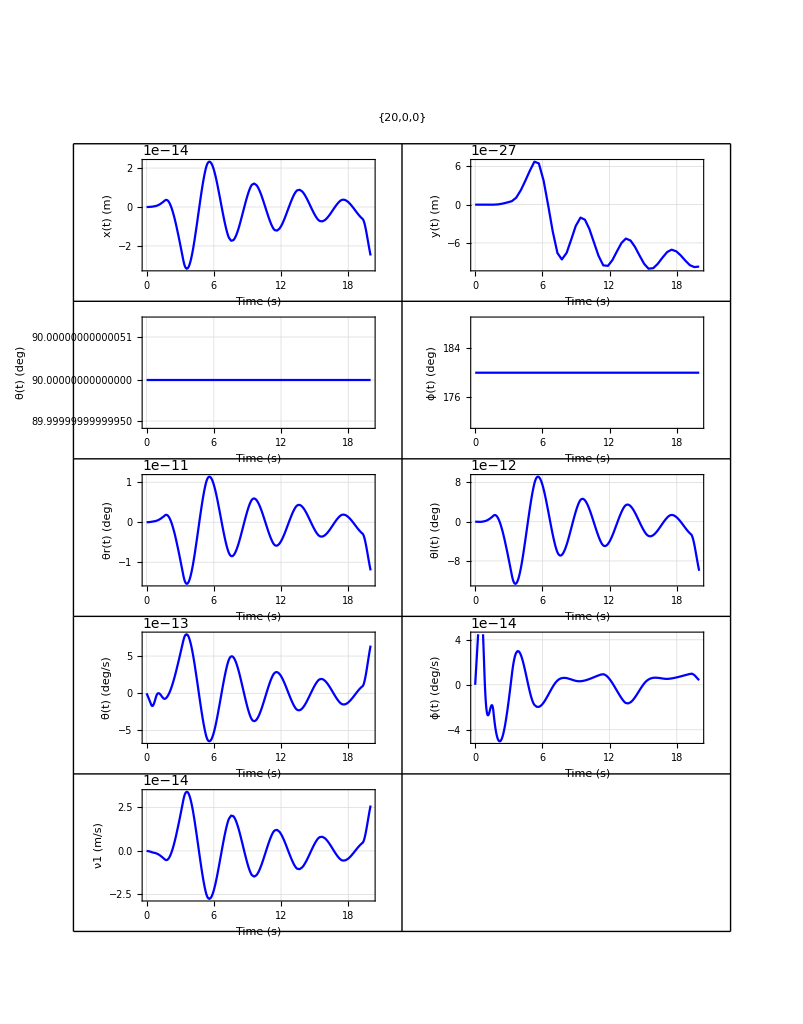

```mathematica
showEgoDynamicSolved[20Degree,0,0]
```

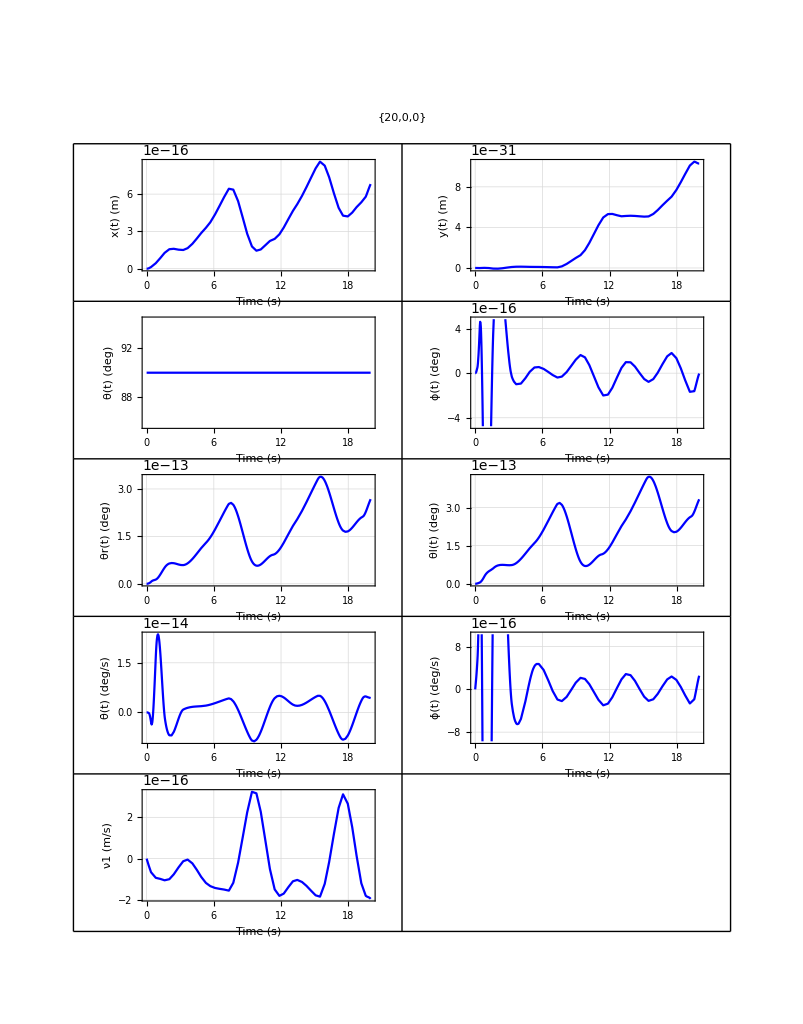

## Static Equations

## Declaration Equations

### Forces

```mathematica
F[Fx_,Fy_,Fz_]:={0,0,0};
τr[τrx_]:={τrx,0,0};
τl[τlx_]:={τlx,0,0};
```

In frame {B’}

```mathematica
Fatt[Fa_]:= {0,Fa, 0};
Normf[NN_]:={0,0,NN};
```

In frame {B}

```mathematica
Pc:= {0,0,-mc g}  (*Weight body*)
Pw:={0,0,-mr g}   (*Weight wheel*)
```

### Static Equations - Frame {S}

```mathematica
Rr[Rrx_,Rry_,Rrz_]:={Rrx,Rry,Rrz};
Rl[Rlx_,Rly_,Rlz_]:={Rlx,Rly,Rlz};
```

```mathematica
Mr[Mry_,Mrz_]:={0,Mry,Mrz};
Ml[Mly_,Mlz_]:={0,Mly,Mlz};
```

#### Right Wheel Equations

```mathematica
ForceRightWheel[α_,θ_,Rrx_,Rry_,Rrz_,Fa_,NN_]:=Rsi[α].Rsb[θ].(Fatt[Fa]+Normf[NN])+Rr[Rrx,Rry,Rrz]+Pw;
MomentRightWheel[α_,θ_,Mry_,Mrz_,τrx_,Fa_,NN_,Rrx_,Rry_,Rrz_,ϕ_]:=Rsi[α].Rsb[θ].τr[τrx]+Rsi[α].Rsb[θ].Mr[Mry,Mrz]+Cross[Rsi[α].Rsb[θ].Rbc[ϕ-α].{l,0,-L}+Rsi[α].Rsb[θ].{0,0,-r},
Rsi[α].Rsb[θ].(Fatt[Fa]+Normf[NN])]+Cross[Rsi[α].Rsb[θ].Rbc[ϕ-α].{l,0,-L},Rr[Rrx,Rry,Rrz]+Pw]
```

#### Left Wheel Equations

```mathematica
ForceLeftWheel[α_,θ_,Rlx_,Rly_,Rlz_,Fa_,NN_]:=Rsi[α].Rsb[θ].(Fatt[Fa]+Normf[NN])+Rl[Rlx,Rly,Rlz]+Pw;
 MomentLeftWheel[α_,θ_,Mly_,Mlz_,τlx_,Fa_,NN_,Rlx_,Rly_,Rlz_,ϕ_]:=Rsi[α].Rsb[θ].τl[τlx]+Rsi[α].Rsb[θ].Ml[Mly,Mlz]+Cross[Rsi[α].Rsb[θ].Rbc[ϕ-α].{-l,0,-L}+Rsi[α].Rsb[θ].{0,0,-r},
Rsi[α].Rsb[θ].(Fatt[Fa]+Normf[NN])]+Cross[Rsi[α].Rsb[θ].Rbc[ϕ-α].{-l,0,-L},Rl[Rlx,Rly,Rlz]+Pw]
```

#### Body Equations

```mathematica
ForceBody[Rrx_,Rry_,Rrz_,Rlx_,Rly_,Rlz_]:=Pc+Rr[Rrx,Rry,Rrz]+Rl[Rlx,Rly,Rlz]
```

```mathematica
MomentBody[α_,θ_,ϕ_,Mry_,Mrz_,Mly_,Mlz_,Rrx_,Rry_,Rrz_,Rlx_,Rly_,Rlz_]:=Rsi[α].Rsb[θ].(Mr[Mry,Mrz]+Ml[Mly,Mlz])+Cross[Rsi[α].Rsb[θ].Rbc[ϕ-α].{l,0,-L},Rr[Rrx,Rry,Rrz]]+Cross[Rsi[α].Rsb[θ].Rbc[ϕ-α].{-l,0,-L},Rl[Rlx,Rly,Rlz]]
```

### Equations Visualization

```mathematica
ForceRightWheel[α,θ,Rrx,Rry,Rrz,Fa,NN]//FullSimplify//MatrixForm
MomentRightWheel[α,θ,Mry,Mrz,τrx,Fa,NN,Rrx,Rry,Rrz,ϕ]//FullSimplify//MatrixForm
```

(Rrx-Fa Sin[θ]
Rry+Fa Cos[α] Cos[θ]-NN Sin[α]
-g mr+Rrz+NN Cos[α]+Fa Cos[θ] Sin[α])

(L Cos[α-ϕ] (Rry Cos[α]+(-g mr+Rrz) Sin[α])-(Mry-l NN+l (g mr-Rrz) Cos[α]+l Rry Sin[α]) Sin[θ]+Cos[θ] (Fa r+τrx+Fa L Cos[α-ϕ]+L (-NN+g mr Cos[α]-Rrz Cos[α]+Rry Sin[α]) Sin[α-ϕ])
-Fa l Cos[θ]^2 Sin[α]-Sin[α] (Mrz+l Sin[θ] (-Rrx+Fa Sin[θ]))+L (g mr-Rrz) Sin[θ] Sin[α-ϕ]+Cos[θ] (g l mr-l Rrz+(Mry-l NN) Cos[α]-L Rrx Sin[α] Sin[α-ϕ])+Cos[α] (L Cos[α-ϕ] (-Rrx+Fa Sin[θ])+Sin[θ] (Fa r+τrx-L NN Sin[α-ϕ]))
Cos[θ] (l Rry+(Mry-l NN) Sin[α])+Sin[α] ((Fa r+τrx) Sin[θ]+L Cos[α-ϕ] (-Rrx+Fa Sin[θ]))+L (Rry-NN Sin[α]) Sin[θ] Sin[α-ϕ]+Cos[α] (Fa l+Mrz-l Rrx Sin[θ]+L Rrx Cos[θ] Sin[α-ϕ]))

```mathematica
ForceLeftWheel[α,θ,Rlx,Rly,Rlz,Fa,NN]//FullSimplify//MatrixForm
MomentLeftWheel[α,θ,Mly,Mlz,τlx,Fa,NN,Rlx,Rly,Rlz,ϕ]//FullSimplify//MatrixForm
```

(Rlx-Fa Sin[θ]
Rly+Fa Cos[α] Cos[θ]-NN Sin[α]
-g mr+Rlz+NN Cos[α]+Fa Cos[θ] Sin[α])

(L Cos[α-ϕ] (Rly Cos[α]+(-g mr+Rlz) Sin[α])-(Mly+l NN+l (-g mr+Rlz) Cos[α]-l Rly Sin[α]) Sin[θ]+Cos[θ] (Fa r+τlx+Fa L Cos[α-ϕ]+L (-NN+g mr Cos[α]-Rlz Cos[α]+Rly Sin[α]) Sin[α-ϕ])
Fa l Cos[θ]^2 Sin[α]-Sin[α] (Mlz+l Sin[θ] (Rlx-Fa Sin[θ]))+L (g mr-Rlz) Sin[θ] Sin[α-ϕ]+Cos[θ] (-g l mr+l Rlz+(Mly+l NN) Cos[α]-L Rlx Sin[α] Sin[α-ϕ])+Cos[α] (L Cos[α-ϕ] (-Rlx+Fa Sin[θ])+Sin[θ] (Fa r+τlx-L NN Sin[α-ϕ]))
Cos[θ] (-l Rly+(Mly+l NN) Sin[α])+Sin[α] ((Fa r+τlx) Sin[θ]+L Cos[α-ϕ] (-Rlx+Fa Sin[θ]))+L (Rly-NN Sin[α]) Sin[θ] Sin[α-ϕ]+Cos[α] (-Fa l+Mlz+l Rlx Sin[θ]+L Rlx Cos[θ] Sin[α-ϕ]))

```mathematica
ForceBody[Rrx,Rry,Rrz,Rlx,Rly,Rlz]//FullSimplify//MatrixForm
MomentBody[α,θ,ϕ,Mry,Mrz,Mly,Mlz,Rrx,Rry,Rrz,Rlx,Rly,Rlz]//FullSimplify//MatrixForm
```

(Rlx+Rrx
Rly+Rry
-g mc+Rlz+Rrz)

(L Cos[α-ϕ] ((Rly+Rry) Cos[α]+(Rlz+Rrz) Sin[α])-(Mly+Mry+l (Rlz-Rrz) Cos[α]+l (-Rly+Rry) Sin[α]) Sin[θ]+L Cos[θ] (-(Rlz+Rrz) Cos[α]+(Rly+Rry) Sin[α]) Sin[α-ϕ]
-L (Rlx+Rrx) Cos[α] Cos[α-ϕ]-Sin[α] (Mlz+Mrz+l (Rlx-Rrx) Sin[θ])-L (Rlz+Rrz) Sin[θ] Sin[α-ϕ]+Cos[θ] (l (Rlz-Rrz)+(Mly+Mry) Cos[α]-L (Rlx+Rrx) Sin[α] Sin[α-ϕ])
-L (Rlx+Rrx) Cos[α-ϕ] Sin[α]+Cos[θ] (l (-Rly+Rry)+(Mly+Mry) Sin[α])+Cos[α] (Mlz+Mrz+l (Rlx-Rrx) Sin[θ])+L ((Rlx+Rrx) Cos[α] Cos[θ]+(Rly+Rry) Sin[θ]) Sin[α-ϕ])

### Static Solution Function

```mathematica
MomentRightWheel[α,θ,Mry,Mrz,τrx,μ NN,NN,Rrx,Rry,Rrz,ϕ]//MatrixForm;
```

```mathematica
MomentLeftWheel[α,θ,Mly,Mlz,τlx,μ NN,NN,Rlx,Rly,Rlz,ϕ]//MatrixForm;
```

```mathematica
solverForcesStaticEquation[α_,ϕ_,θ_,μ_]:=Solve[{
ForceRightWheel[α,θ,Rrx,Rry,Rrz,μ NN Sign[α],NN]==0,
MomentRightWheel[α,θ,Mry,Mrz,τrx,μ NN Sign[α],NN,Rrx,Rry,Rrz,ϕ]==0,
ForceLeftWheel[α,θ,Rlx,Rly,Rlz,μ NN Sign[α],NN]==0,
MomentLeftWheel[α,θ,Mly,Mlz,τlx,μ NN Sign[α],NN,Rlx,Rly,Rlz,ϕ]==0,
ForceBody[Rrx,Rry,Rrz,Rlx,Rly,Rlz]==0,
MomentBody[α,θ,ϕ,Mry,Mrz,Mly,Mlz,Rrx,Rry,Rrz,Rlx,Rly,Rlz]==0
}/.egoParameters
,{τlx,τrx,NN,Mry,Mrz,Mly,Mlz,Rrx,Rry,Rrz,Rlx,Rly,Rlz}
]//Flatten//FullSimplify
```

## 3D Visualization of Static Solutions

```mathematica
Manipulate[
showEgoStaticSolved[degToRad[α],degToRad[ϕ],degToRad[θ],μ,scale],
{{scale,5,"scale (m)"},2,10,Appearance->{"Labeled"}},
{{α,0,"α (deg)"},0,90,Appearance->{"Labeled"}},
{{ϕ,0,"ϕ (deg)"},-180,180,Appearance->{"Labeled"}},
{{θ,0,"θ (deg)"},-180,180,Appearance->{"Labeled"}},
{{μ,1,"Attrito"},0,2,Appearance->{"Labeled"}}
]
```

# Robot Simulator - Data From Matlab

### Import .dat files

```mathematica
directoryMatlab:="C:\\Users\\stefa\\Desktop\\ego\\mathematica\\ego_export\\";
```

```mathematica
setIimageSize=Medium;
```

```mathematica
importData:={
xMatlab=Transpose[Import[StringJoin[directoryMatlab,"x.dat"]]]//Flatten;
yMatlab=Transpose[Import[StringJoin[directoryMatlab,"y.dat"]]]//Flatten;
θMatlab=Transpose[Import[StringJoin[directoryMatlab,"theta.dat"]]]//Flatten;
ϕMatlab=(Transpose[Import[StringJoin[directoryMatlab,"phi.dat"]]]//Flatten);
θrMatlab=Transpose[Import[StringJoin[directoryMatlab,"thetar.dat"]]]//Flatten;
θlMatlab=Transpose[Import[StringJoin[directoryMatlab,"thetal.dat"]]]//Flatten;
ν1Matlab = Transpose[Import[StringJoin[directoryMatlab,"nu1.dat"]]]//Flatten;
ν2Matlab = Transpose[Import[StringJoin[directoryMatlab,"nu2.dat"]]]//Flatten;
ν3Matlab = Transpose[Import[StringJoin[directoryMatlab,"nu3.dat"]]]//Flatten;
ν1IntMatlab = Transpose[Import[StringJoin[directoryMatlab,"nu1int.dat"]]]//Flatten;
τrMatlab = Transpose[Import[StringJoin[directoryMatlab,"taur.dat"]]]//Flatten;
τlMatlab = Transpose[Import[StringJoin[directoryMatlab,"taul.dat"]]]//Flatten;
αMatlab=Import[StringJoin[directoryMatlab,"alpha.dat"]]//Flatten//First;
}
```

### Analyze file

```mathematica
fileLen:=xMatlab//Dimensions//First
```

```mathematica
θzero:=θMatlab[[1]];
ϕzero:=ϕMatlab[[1]];
```

### Declaration Functions

#### Plot

```mathematica
plotResults[x_,y_,θ_,ϕ_,θr_,θl_,ν1_,ν2_,ν3_,ν1dot_,τr_,τl_]:=Module[{},
GraphicsGrid[
{
{
ListLinePlot[Transpose[{Range[fileLen],x}], PlotStyle->{Blue},ImageSize->setIimageSize,AspectRatio->1/2,AxesLabel->Automatic,PlotTheme->"Scientific",GridLines->Automatic,FrameLabel->{Style["Time (s)",FontSize->14],Style["x(t)\n(m)",FontSize->18]},RotateLabel->False,PlotRange->All
,FrameTicks->{{Automatic,Automatic},{{{0,"0"},{100,"10"},{200,"20"},{50,"5"},{150,"15"}},None}}

],

ListLinePlot[Transpose[{Range[fileLen],y}],PlotStyle->{Blue},ImageSize->setIimageSize,AspectRatio->1/2,AxesLabel->Automatic,PlotTheme->"Scientific",GridLines->Automatic,FrameLabel->{Style["Time (s)",FontSize->14],Style["y(t)\n(m)",FontSize->18]},RotateLabel->False,PlotRange->All
,FrameTicks->{{Automatic,Automatic},{{{0,"0"},{100,"10"},{200,"20"},{50,"5"},{150,"15"}},None}}

],

ListLinePlot[Transpose[{Range[fileLen],radToDeg[θ]}],PlotStyle->{Blue},ImageSize->setIimageSize,AspectRatio->1/2,AxesLabel->Automatic,PlotTheme->"Scientific",GridLines->Automatic,FrameLabel->{Style["Time (s)",FontSize->14],Style["θ(t)\n(deg)",FontSize->18]},RotateLabel->False,PlotRange->All
,FrameTicks->{{Automatic,Automatic},{{{0,"0"},{100,"10"},{200,"20"},{50,"5"},{150,"15"}},None}}

]

},
{
ListLinePlot[Transpose[{Range[fileLen],radToDeg[ϕ]}],PlotStyle->{Blue},ImageSize->setIimageSize,AspectRatio->1/2,AxesLabel->Automatic,PlotTheme->"Scientific",GridLines->Automatic,FrameLabel->{Style["Time (s)",FontSize->14],Style["ϕ(t)\n(deg)",FontSize->18]},RotateLabel->False,PlotRange->All
,FrameTicks->{{Automatic,Automatic},{{{0,"0"},{100,"10"},{200,"20"},{50,"5"},{150,"15"}},None}}

],

ListLinePlot[Transpose[{Range[fileLen],radToDeg[θr]}],PlotStyle->{Blue},ImageSize->setIimageSize,AspectRatio->1/2,AxesLabel->Automatic,PlotTheme->"Scientific",GridLines->Automatic,FrameLabel->{Style["Time (s)",FontSize->14],Style["θr(t)\n(deg)",FontSize->18]},RotateLabel->False,PlotRange->All
,FrameTicks->{{Automatic,Automatic},{{{0,"0"},{100,"10"},{200,"20"},{50,"5"},{150,"15"}},None}}

],

ListLinePlot[Transpose[{Range[fileLen],radToDeg[θl]}],PlotStyle->{Blue},ImageSize->setIimageSize,AspectRatio->1/2,AxesLabel->Automatic,PlotTheme->"Scientific",GridLines->Automatic,FrameLabel->{Style["Time (s)",FontSize->14],Style["θl(t)\n(deg)",FontSize->18]},RotateLabel->False,PlotRange->All
,FrameTicks->{{Automatic,Automatic},{{{0,"0"},{100,"10"},{200,"20"},{50,"5"},{150,"15"}},None}}

]

},
{
ListLinePlot[Transpose[{Range[fileLen],ν1}],PlotStyle->{Blue},ImageSize->setIimageSize,AspectRatio->1/2,AxesLabel->Automatic,PlotTheme->"Scientific",GridLines->Automatic,FrameLabel->{Style["Time (s)",FontSize->14],Style["ν1(t)\n(m/s)",FontSize->18]},RotateLabel->False,PlotRange->All
,FrameTicks->{{Automatic,Automatic},{{{0,"0"},{100,"10"},{200,"20"},{50,"5"},{150,"15"}},None}}

],
ListLinePlot[Transpose[{Range[fileLen],radToDeg[ν2]}],PlotStyle->{Blue},ImageSize->setIimageSize,AspectRatio->1/2,AxesLabel->Automatic,PlotTheme->"Scientific",GridLines->Automatic,FrameLabel->{Style["Time (s)",FontSize->14],Style["θ̇(t)\n(deg/s)",FontSize->18]},RotateLabel->False,PlotRange->All
,FrameTicks->{{Automatic,Automatic},{{{0,"0"},{100,"10"},{200,"20"},{50,"5"},{150,"15"}},None}}

],

ListLinePlot[Transpose[{Range[fileLen],radToDeg[ν3]}],PlotStyle->{Blue},ImageSize->setIimageSize,AspectRatio->1/2,AxesLabel->Automatic,PlotTheme->"Scientific",GridLines->Automatic,FrameLabel->{Style["Time (s)",FontSize->14],Style["ϕ̇(t)\n(deg/s)",FontSize->18]},RotateLabel->False,PlotRange->All
,FrameTicks->{{Automatic,Automatic},{{{0,"0"},{100,"10"},{200,"20"},{50,"5"},{150,"15"}},None}}

]

},

{
ListLinePlot[Transpose[{Range[fileLen],τr}],PlotStyle->{Blue},ImageSize->setIimageSize,AspectRatio->1/2,AxesLabel->Automatic,PlotTheme->"Scientific",GridLines->Automatic,FrameLabel->{Style["Time (s)",FontSize->14],Style["τr(t)\n(N*m)",FontSize->18]},RotateLabel->False,PlotRange->All
,FrameTicks->{{Automatic,Automatic},{{{0,"0"},{100,"10"},{200,"20"},{50,"5"},{150,"15"}},None}}

],
ListLinePlot[Transpose[{Range[fileLen],τl}],PlotStyle->{Blue},ImageSize->setIimageSize,AspectRatio->1/2,AxesLabel->Automatic,PlotTheme->"Scientific",GridLines->Automatic,FrameLabel->{Style["Time (s)",FontSize->14],Style["τl(t)\n(N*m)",FontSize->18]},RotateLabel->False,PlotRange->All
,FrameTicks->{{Automatic,Automatic},{{{0,"0"},{100,"10"},{200,"20"},{50,"5"},{150,"15"}},None}}

],
ListLinePlot[Transpose[{Range[fileLen],ν1dot}],PlotStyle->{Blue},ImageSize->setIimageSize,AspectRatio->1/2,AxesLabel->Automatic,PlotTheme->"Scientific",GridLines->Automatic,FrameLabel->{Style["Time (s)",FontSize->14],Style["OverDot[ν1](t)\n(m)",FontSize->18]},RotateLabel->False,PlotRange->All
,FrameTicks->{{Automatic,Automatic},{{{0,"0"},{100,"10"},{200,"20"},{50,"5"},{150,"15"}},None}}

]

}


},Frame->All,Spacings->Scaled[0.15],PlotLabel->Style[{"α=",radToDeg[αMatlab],"°"},FontSize->18]
]
]
```

#### 3D Simulator

```mathematica
Clear[showEgoDynamicFromMatlab]
```

```mathematica
showEgoDynamicFromMatlab:=Module[{},
importData;
Return[{
Manipulate[
Column[{
Grid[{
{StringJoin["Slope: ",ToString[radToDeg[αMatlab]],"°"]},
{StringJoin["Initial pitch: ",ToString[radToDeg[ϕzero]],"°"]},
{StringJoin["Initial yaw: ",ToString[radToDeg[θzero]],"°"]}
}
],
Graphics3D[{
versor[scale/5],
rampa[scale,0,Red],
rampa[scale,αMatlab],
ego[xMatlab[[tt]]+2,yMatlab[[tt]]+scale 2/4,θMatlab[[tt]], ϕMatlab[[tt]],θrMatlab[[tt]],θlMatlab[[tt]],αMatlab]
(*ego[xMatlab[[tt]]+2.5, yMatlab[[tt]]+scale 2/4,degToRad[0],degToRad[20],θrMatlab[[tt]],θlMatlab[[tt]],αMatlab]*)
(*,
ego[xMatlab[[tt]]+1.5, yMatlab[[tt]]+scale 2/4,degToRad[0], degToRad[23],θrMatlab[[tt]],θlMatlab[[tt]],αMatlab],
ego[xMatlab[[tt]]+3.5, yMatlab[[tt]]+scale 2/4,degToRad[0], -degToRad[23],θrMatlab[[tt]],θlMatlab[[tt]],αMatlab]
*)
}(*,limitAxes[scale,αMatlab]*),Axes->True,ImageSize->800,Boxed->False,ViewPoint->{4, -2, 1.3}
]
},Alignment->Center
],
{{scale,5, "Area size"},2,15,1,Appearance->{"Labeled"}},
{{tt,1,"Time t (sec)"},1,fileLen,1,Appearance->{"Labeled", "Open"}(*,AnimationRate->10*)}
(*,ContentSize->{800,600}*)
]

(*,plotResults[xMatlab,yMatlab,θMatlab,ϕMatlab,θrMatlab,θlMatlab,ν1Matlab,ν2Matlab,ν3Matlab,ν1IntMatlab,τrMatlab,τlMatlab]*)

}]
];
```

### Visualization

```mathematica
showEgoDynamicFromMatlab
```

Import::nffil: File not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[$Failed].

{}